```mathematica
xxx=ToExpression[StringReplace[xx,{"\n"->","}]]
```

```mathematica
Map[Det,xxx]
```

```mathematica
Tally[%]
```

{{0,89570},{-1,9678},{1,9666}}

```mathematica
xxx[[12]]
```

{{10,1,3,9},{14,12,11,5},{13,8,6,16},{2,15,7,4}}

```mathematica
x4=Select[xxx,Det[#]≠0&]
```

```mathematica
Length[Out[8]]
```

19344

```mathematica
tf[x_]:=Piecewise[{{1, x==True}, {0, x≠True}}];
dmat=Monitor[Table[(tf[i≠j])*tf[GroupElementQ[PermutationGroup[{Out[8][[i]]}],Out[8][[j]]]],{i,1,19344},{j,1,19344}],{i,j}]
```

```mathematica
x=Select[ReadList["/Users/michaelklein/Downloads/mat4tot.log.txt"],Det[#]≠0&]
```

{{{12,16,14,15},{13,7,8,10},{2,11,5,1},{3,4,6,9}},{{10,1,3,9},{14,12,11,5},{13,8,6,16},{2,15,7,4}},{{15,6,13,1},{5,10,16,14},{2,9,8,7},{11,3,12,4}},{{7,5,12,1},{6,3,2,8},{16,15,14,9},{11,10,13,4}},{{12,6,11,10},{2,3,16,7},{13,1,15,9},{4,5,14,8}},«19335»,{{15,4,9,14},{2,16,13,10},{11,5,8,12},{3,6,7,1}},{{15,4,11,13},{16,3,9,8},{12,6,14,7},{2,5,10,1}},{{2,16,8,9},{10,7,4,1},{13,11,6,3},{12,14,5,15}},{{10,16,8,11},{5,13,9,15},{14,7,4,6},{2,12,3,1}}}

```mathematica
Length[x]
```

19344

```mathematica
xx=Map[FindPermutation[Flatten[#]]&,x]
```

{Cycles[{{1,12},{2,9,16},{3,13,5,11,10,8,7,6,15,4,14}}],Cycles[{{1,2,13,9,4,16,12,6,11,7,15,14,5,8,10}}],Cycles[{{1,4,16,7,12,15},{2,9,10,6},{3,14,8,11,13}}],Cycles[{{1,4,16,9,12,3,6,5,2,7},{10,14,11,13,15}}],«19336»,Cycles[{{1,16,6,14,4,2,5,10,8,11,9,3,13,7,15}}],Cycles[{{1,16,5,14,11,3,6,10,15},{2,13,4},{7,12,9}}],Cycles[{{1,8,3,12,13,9,4,7,6,11,10,5,15,16,2}}],Cycles[{{1,16,2,13,6,12,14,9,7,10},{3,15,8},{4,11}}]}

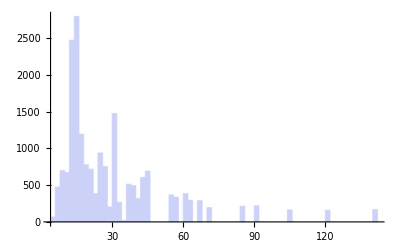

```mathematica
Histogram[Map[PermutationOrder,xx]]
```

```mathematica
Mean[Map[PermutationOrder,xx]]
```

93585/3224

```mathematica
N[%]
```

29.0276

```mathematica
tf[x_]:=Piecewise[{{1, x==True}, {0, x≠True}}];
Timing[Monitor[Table[(tf[i≠j])*tf[GroupElementQ[PermutationGroup[{xx[[i]]}],xx[[j]]]],{i,1,1},{j,1,19344}],{i,j}]]
```

```mathematica
Total[Out[15][[2,1]]]
```

0

```mathematica
Timing[Monitor[Table[(tf[i≠j])*tf[GroupElementQ[PermutationGroup[{xx[[i]]}],xx[[j]]]],{i,2,2},{j,2,19344}],{i,j}]]
```

```mathematica
Total[Out[21][[2,1]]]
```

0

```mathematica
Timing[Monitor[Table[(tf[i≠j])*tf[GroupElementQ[PermutationGroup[{xx[[i]]}],xx[[j]]]],{i,3,3},{j,4,19344}],{i,j}]]
```

```mathematica
Total[Out[23][[2,1]]]
```

0

```mathematica
d=0;
```

```mathematica
c=3;
```

```mathematica
While[d<1,
d=Total[First[Table[(tf[i≠j])*tf[GroupElementQ[PermutationGroup[{xx[[i]]}],xx[[j]]]],{i,c,c},{j,c+1,19344}]]];
Print[c];
c++]
```

```mathematica
113323
```

```mathematica
Timing[Select[DeleteCases[Delete[GroupElements[PermutationGroup[{Cycles[{{1,12},{2,9,16},{3,13,5,11,10,8,7,6,15,4,14}}]}]],1],Cycles[{{1,12},{2,9,16},{3,13,5,11,10,8,7,6,15,4,14}}]],Abs[Det[Partition[Permute[Range[16],#],4]]]==1&]]
```

{0.003749,{}}

```mathematica
Select[DeleteCases[Delete[GroupElements[PermutationGroup[{Cycles[{{1,7,4,6},{2,9},{3,8,5}}]}]],1],Cycles[{{1,7,4,6},{2,9},{3,8,5}}]],Abs[Det[Partition[Permute[Range[9],#],3]]]==1&]
```

{Cycles[{{3,5,8}}]}

```mathematica
wch[cy_]:=Select[DeleteCases[Delete[GroupElements[PermutationGroup[{cy}]],1],cy],Abs[Det[Partition[Permute[Range[16],#],4]]]==1&]
```

```mathematica
Timing[Monitor[Table[wch[xx[[i]]],{i,1,19344}],i]]
```

```mathematica
DeleteCases[Last[{{}, {{54.12904900000001,{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},«19220»,{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{Cycles[{{1,8,6,15,13,10,14},{2,12,16,7,5},{3,9,4,11}}]},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}}}, {}}],{}]
```

{{Cycles[{{5,14},{6,9,13,7,8}}]},{Cycles[{{1,7,5,3,16,9,13,15,10,8,6,2,4}}]},{Cycles[{{3,12,8},{4,5,16},{11,13,14}}]},{Cycles[{{1,8,14,11,2,10,15,13},{3,4,16,5,7,9,12,6}}]},{Cycles[{{1,9},{2,8,11,13,12,4,5,7,16},{3,6},{10,14,15}}]},{Cycles[{{1,6,11},{2,12,16,7,3,15,9,8,10,13,5}}]},{Cycles[{{1,11,5,8,9,12,2,3,10,15,13},{4,16,6,7,14}}]},{Cycles[{{3,4,10,9,11,7,6}}]},{Cycles[{{3,6,13,10,12},{4,9,11}}]},{Cycles[{{1,12,13},{2,15,5},{3,9,16,11,7},{4,14,8},{6,10}}]},{Cycles[{{1,4,8,9,5,10,7,6,12},{2,16,11},{3,15,13}}]},{Cycles[{{1,4,8,6,11,9,3},{2,5,12,14,16},{10,15}}]},{Cycles[{{3,15,9,4},{5,11,6,16,8,13,10}}]},{Cycles[{{2,6,15,5,16,3},{4,10,12,13,8,14,11,7,9}}]},{Cycles[{{1,2,9},{3,14,4},{5,12,7,6,15,16,8},{10,13,11}}]},{Cycles[{{5,11,13,8,15,14,9,7}}]},{Cycles[{{1,8,13,14,11,15,12,16,10,9,2,3,4}}]},{Cycles[{{1,7,3,15,16,9,5},{6,13},{10,14},{11,12}}]},{Cycles[{{3,4,8,6,16,13,10},{5,11,15,9}}]},{Cycles[{{1,3},{7,8},{11,14}}]},{Cycles[{{1,6,11,16},{3,7,9,8},{4,10,5,12,15,14,13}}]},{Cycles[{{1,16,5,8,12,15,9},{3,10,14,13,7}}]},{Cycles[{{1,7},{5,10},{6,13},{8,15},{9,12,16,11,14}}]},{Cycles[{{1,12,5,10,6,7,15},{2,14},{3,11,8,13,16},{4,9}}]},{Cycles[{{2,14,15,12,4,8,10,13,5},{3,16,11,7}}]},{Cycles[{{1,2,4},{6,8,10,16,9,12,11,15,13}}]},{Cycles[{{1,15,10,13,6,8,4,9,7},{2,11,14},{3,16,5,12}}]},{Cycles[{{1,5},{2,13,12,15,6,4},{3,10},{7,16},{8,14},{9,11}}]},{Cycles[{{1,4,5},{6,13,8},{7,14,15},{11,12,16}}]},{Cycles[{{1,10,11,16,4,6,15},{2,9,8,12,3,13,7,5,14}}]},{Cycles[{{1,2,14,16,10,11,8,5,7,13,15,9,4}}]},{Cycles[{{1,7,14,5,4},{2,15,3,6,9}}]},{Cycles[{{1,16,11,7,2,15,10},{3,14,9,13},{4,8,5},{6,12}}]},{Cycles[{{1,4},{3,6,7,10,12,16,5},{8,13},{9,11},{14,15}}]},{Cycles[{{1,14,15,12,2,13,11,3,10},{5,9}}]},{Cycles[{{1,16},{2,12},{3,4},{6,9,7,11,15},{8,10},{13,14}}]},{Cycles[{{1,16,15,11,4,9,10,7,2,5,6,13,3}}]},{Cycles[{{1,13,4,6,16,11,14,2,7,8,9,3,10},{5,15,12}}]},{Cycles[{{1,9,12,14,16,4,7,11},{2,5,8,10,15,13,3,6}}]},{Cycles[{{1,10,8},{2,13,4},{3,5,11},{7,12,9}}]},{Cycles[{{1,11,16,3},{2,8},{4,13,12,15,6,10,7,9,14}}]},{Cycles[{{1,5,2,6,14,12,7},{8,16,11,15,9}}]},{Cycles[{{1,2,6,12,14,5,13,7,16}}]},{Cycles[{{2,9,13,3,12},{4,10},{6,11},{7,14},{8,16}}]},{Cycles[{{1,8,6,15,13,10,14},{2,12,16,7,5},{3,9,4,11}}]}}

```mathematica
Table[Position[Out[128],i],{i,{{Cycles[{{5,14},{6,9,13,7,8}}]},{Cycles[{{1,7,5,3,16,9,13,15,10,8,6,2,4}}]},{Cycles[{{3,12,8},{4,5,16},{11,13,14}}]},{Cycles[{{1,8,14,11,2,10,15,13},{3,4,16,5,7,9,12,6}}]},{Cycles[{{1,9},{2,8,11,13,12,4,5,7,16},{3,6},{10,14,15}}]},{Cycles[{{1,6,11},{2,12,16,7,3,15,9,8,10,13,5}}]},{Cycles[{{1,11,5,8,9,12,2,3,10,15,13},{4,16,6,7,14}}]},{Cycles[{{3,4,10,9,11,7,6}}]},{Cycles[{{3,6,13,10,12},{4,9,11}}]},{Cycles[{{1,12,13},{2,15,5},{3,9,16,11,7},{4,14,8},{6,10}}]},{Cycles[{{1,4,8,9,5,10,7,6,12},{2,16,11},{3,15,13}}]},{Cycles[{{1,4,8,6,11,9,3},{2,5,12,14,16},{10,15}}]},{Cycles[{{3,15,9,4},{5,11,6,16,8,13,10}}]},{Cycles[{{2,6,15,5,16,3},{4,10,12,13,8,14,11,7,9}}]},{Cycles[{{1,2,9},{3,14,4},{5,12,7,6,15,16,8},{10,13,11}}]},{Cycles[{{5,11,13,8,15,14,9,7}}]},{Cycles[{{1,8,13,14,11,15,12,16,10,9,2,3,4}}]},{Cycles[{{1,7,3,15,16,9,5},{6,13},{10,14},{11,12}}]},{Cycles[{{3,4,8,6,16,13,10},{5,11,15,9}}]},{Cycles[{{1,3},{7,8},{11,14}}]},{Cycles[{{1,6,11,16},{3,7,9,8},{4,10,5,12,15,14,13}}]},{Cycles[{{1,16,5,8,12,15,9},{3,10,14,13,7}}]},{Cycles[{{1,7},{5,10},{6,13},{8,15},{9,12,16,11,14}}]},{Cycles[{{1,12,5,10,6,7,15},{2,14},{3,11,8,13,16},{4,9}}]},{Cycles[{{2,14,15,12,4,8,10,13,5},{3,16,11,7}}]},{Cycles[{{1,2,4},{6,8,10,16,9,12,11,15,13}}]},{Cycles[{{1,15,10,13,6,8,4,9,7},{2,11,14},{3,16,5,12}}]},{Cycles[{{1,5},{2,13,12,15,6,4},{3,10},{7,16},{8,14},{9,11}}]},{Cycles[{{1,4,5},{6,13,8},{7,14,15},{11,12,16}}]},{Cycles[{{1,10,11,16,4,6,15},{2,9,8,12,3,13,7,5,14}}]},{Cycles[{{1,2,14,16,10,11,8,5,7,13,15,9,4}}]},{Cycles[{{1,7,14,5,4},{2,15,3,6,9}}]},{Cycles[{{1,16,11,7,2,15,10},{3,14,9,13},{4,8,5},{6,12}}]},{Cycles[{{1,4},{3,6,7,10,12,16,5},{8,13},{9,11},{14,15}}]},{Cycles[{{1,14,15,12,2,13,11,3,10},{5,9}}]},{Cycles[{{1,16},{2,12},{3,4},{6,9,7,11,15},{8,10},{13,14}}]},{Cycles[{{1,16,15,11,4,9,10,7,2,5,6,13,3}}]},{Cycles[{{1,13,4,6,16,11,14,2,7,8,9,3,10},{5,15,12}}]},{Cycles[{{1,9,12,14,16,4,7,11},{2,5,8,10,15,13,3,6}}]},{Cycles[{{1,10,8},{2,13,4},{3,5,11},{7,12,9}}]},{Cycles[{{1,11,16,3},{2,8},{4,13,12,15,6,10,7,9,14}}]},{Cycles[{{1,5,2,6,14,12,7},{8,16,11,15,9}}]},{Cycles[{{1,2,6,12,14,5,13,7,16}}]},{Cycles[{{2,9,13,3,12},{4,10},{6,11},{7,14},{8,16}}]},{Cycles[{{1,8,6,15,13,10,14},{2,12,16,7,5},{3,9,4,11}}]}}}]
```

```mathematica
Map[Last[Flatten[#]]&,{{{2,128}},{{2,166}},{{2,212}},{{2,999}},{{2,1007}},{{2,1092}},{{2,1235}},{{2,1503}},{{2,1572}},{{2,1590}},{{2,2101}},{{2,2133}},{{2,2465}},{{2,2706}},{{2,2822}},{{2,3210}},{{2,3990}},{{2,4980}},{{2,5088}},{{2,5654}},{{2,6628}},{{2,6875}},{{2,7179}},{{2,7637}},{{2,7672}},{{2,9891}},{{2,11150}},{{2,11283}},{{2,11486}},{{2,11740}},{{2,12860}},{{2,15223}},{{2,15467}},{{2,15654}},{{2,16580}},{{2,17004}},{{2,17119}},{{2,17210}},{{2,17614}},{{2,17825}},{{2,17935}},{{2,18371}},{{2,18532}},{{2,18729}},{{2,19298}}}]
```

{128,166,212,999,1007,1092,1235,1503,1572,1590,2101,2133,2465,2706,2822,3210,3990,4980,5088,5654,6628,6875,7179,7637,7672,9891,11150,11283,11486,11740,12860,15223,15467,15654,16580,17004,17119,17210,17614,17825,17935,18371,18532,18729,19298}

```mathematica
Table[{xx[[i]],First[wch[xx[[i]]]]},{i,{128,166,212,999,1007,1092,1235,1503,1572,1590,2101,2133,2465,2706,2822,3210,3990,4980,5088,5654,6628,6875,7179,7637,7672,9891,11150,11283,11486,11740,12860,15223,15467,15654,16580,17004,17119,17210,17614,17825,17935,18371,18532,18729,19298}}]
```

{{Cycles[{{1,12,11,4,2,16,15},{5,14},{6,9,13,7,8}}],Cycles[{{5,14},{6,9,13,7,8}}]},{Cycles[{{1,7,5,3,16,9,13,15,10,8,6,2,4},{11,12}}],Cycles[{{1,7,5,3,16,9,13,15,10,8,6,2,4}}]},{Cycles[{{1,9,6,10,2,7},{3,11,5,8,14,4,12,13,16}}],Cycles[{{3,12,8},{4,5,16},{11,13,14}}]},{Cycles[{{1,7,13,5,15,16,10,4,2,3,11,6,14,12,8,9}}],Cycles[{{1,8,14,11,2,10,15,13},{3,4,16,5,7,9,12,6}}]},{Cycles[{{1,3,9,6},{2,4,8,5,11,7,13,16,12},{10,15,14}}],Cycles[{{1,9},{2,8,11,13,12,4,5,7,16},{3,6},{10,14,15}}]},{Cycles[{{1,11,6},{2,12,16,7,3,15,9,8,10,13,5}}],Cycles[{{1,6,11},{2,12,16,7,3,15,9,8,10,13,5}}]},{Cycles[{{1,15,3,12,8,11,13,10,2,9,5},{4,6,14,16,7}}],Cycles[{{1,11,5,8,9,12,2,3,10,15,13},{4,16,6,7,14}}]},{Cycles[{{2,13,8,16,5,12,15,14},{3,9,6,10,7,4,11}}],Cycles[{{3,4,10,9,11,7,6}}]},{Cycles[{{1,2,5,7},{3,12,10,13,6},{4,11,9},{8,15,16,14}}],Cycles[{{3,6,13,10,12},{4,9,11}}]},{Cycles[{{1,2,14,13,5,4,12,15,8},{3,9,16,11,7},{6,10}}],Cycles[{{1,12,13},{2,15,5},{3,9,16,11,7},{4,14,8},{6,10}}]},{Cycles[{{1,6,10,9,4,12,7,5,8},{2,13,11,15,16,3}}],Cycles[{{1,4,8,9,5,10,7,6,12},{2,16,11},{3,15,13}}]},{Cycles[{{1,6,3,8,9,4,11},{2,5,12,14,16},{10,15}}],Cycles[{{1,4,8,6,11,9,3},{2,5,12,14,16},{10,15}}]},{Cycles[{{1,7,14,2,12},{3,15,9,4},{5,16,10,6,13,11,8}}],Cycles[{{3,15,9,4},{5,11,6,16,8,13,10}}]},{Cycles[{{2,3,16,5,15,6},{4,12,8,11,9,10,13,14,7}}],Cycles[{{2,6,15,5,16,3},{4,10,12,13,8,14,11,7,9}}]},{Cycles[{{1,14,2,4,9,3},{5,12,7,6,15,16,8},{10,11,13}}],Cycles[{{1,2,9},{3,14,4},{5,12,7,6,15,16,8},{10,13,11}}]},{Cycles[{{1,3,2,12,4,16,6},{5,7,9,14,15,8,13,11}}],Cycles[{{5,11,13,8,15,14,9,7}}]},{Cycles[{{1,8,13,14,11,15,12,16,10,9,2,3,4},{6,7}}],Cycles[{{1,8,13,14,11,15,12,16,10,9,2,3,4}}]},{Cycles[{{1,3,16,5,7,15,9},{2,8,4},{6,11,10,13,12,14}}],Cycles[{{1,7,3,15,16,9,5},{6,13},{10,14},{11,12}}]},{Cycles[{{3,6,10,8,13,4,16},{5,9,15,11}}],Cycles[{{3,4,8,6,16,13,10},{5,11,15,9}}]},{Cycles[{{1,7,14,3,8,11},{2,5,16,4,9,10,12},{6,15,13}}],Cycles[{{1,3},{7,8},{11,14}}]},{Cycles[{{1,3,16,8,11,9,6,7},{4,13,14,15,12,5,10}}],Cycles[{{1,6,11,16},{3,7,9,8},{4,10,5,12,15,14,13}}]},{Cycles[{{1,5,12,9,16,8,15},{2,4},{3,7,13,14,10}}],Cycles[{{1,16,5,8,12,15,9},{3,10,14,13,7}}]},{Cycles[{{1,13,8,5,7,6,15,10},{3,4},{9,14,11,16,12}}],Cycles[{{1,7},{5,10},{6,13},{8,15},{9,12,16,11,14}}]},{Cycles[{{1,12,5,10,6,7,15},{2,4,14,9},{3,16,13,8,11}}],Cycles[{{1,12,5,10,6,7,15},{2,14},{3,11,8,13,16},{4,9}}]},{Cycles[{{2,5,13,10,8,4,12,15,14},{3,7,11,16}}],Cycles[{{2,14,15,12,4,8,10,13,5},{3,16,11,7}}]},{Cycles[{{1,2,4},{5,7},{6,8,10,16,9,12,11,15,13}}],Cycles[{{1,2,4},{6,8,10,16,9,12,11,15,13}}]},{Cycles[{{1,9,8,13,15,7,4,6,10},{2,11,14},{3,12,5,16}}],Cycles[{{1,15,10,13,6,8,4,9,7},{2,11,14},{3,16,5,12}}]},{Cycles[{{1,10,7,9,8,5,3,16,11,14},{2,4,6,15,12,13}}],Cycles[{{1,5},{2,13,12,15,6,4},{3,10},{7,16},{8,14},{9,11}}]},{Cycles[{{1,14,16,13,5,7,12,6,4,15,11,8},{2,10,9,3}}],Cycles[{{1,4,5},{6,13,8},{7,14,15},{11,12,16}}]},{Cycles[{{1,15,6,4,16,11,10},{2,13,9,7,8,5,12,14,3}}],Cycles[{{1,10,11,16,4,6,15},{2,9,8,12,3,13,7,5,14}}]},{Cycles[{{1,7,16,9,8,2,13,10,4,5,14,15,11},{3,6}}],Cycles[{{1,2,14,16,10,11,8,5,7,13,15,9,4}}]},{Cycles[{{1,6,4,3,5,15,14,2,7,9},{8,10},{11,12,13}}],Cycles[{{1,7,14,5,4},{2,15,3,6,9}}]},{Cycles[{{1,16,11,7,2,15,10},{3,13,9,14},{4,8,5},{6,12}}],Cycles[{{1,16,11,7,2,15,10},{3,14,9,13},{4,8,5},{6,12}}]},{Cycles[{{1,11,8,15,4,9,13,14},{3,10,5,7,16,6,12}}],Cycles[{{1,4},{3,6,7,10,12,16,5},{8,13},{9,11},{14,15}}]},{Cycles[{{1,10,3,11,13,2,12,15,14},{4,8,6,16,7},{5,9}}],Cycles[{{1,14,15,12,2,13,11,3,10},{5,9}}]},{Cycles[{{1,13,8,16,14,10},{2,12},{3,4},{6,9,7,11,15}}],Cycles[{{1,16},{2,12},{3,4},{6,9,7,11,15},{8,10},{13,14}}]},{Cycles[{{1,16,15,11,4,9,10,7,2,5,6,13,3},{8,12}}],Cycles[{{1,16,15,11,4,9,10,7,2,5,6,13,3}}]},{Cycles[{{1,6,14,8,10,4,11,7,3,13,16,2,9},{5,12,15}}],Cycles[{{1,13,4,6,16,11,14,2,7,8,9,3,10},{5,15,12}}]},{Cycles[{{1,13,4,8,12,6,11,15,16,5,9,3,7,10,14,2}}],Cycles[{{1,9,12,14,16,4,7,11},{2,5,8,10,15,13,3,6}}]},{Cycles[{{1,11,8,5,10,3},{2,9,4,12,13,7},{6,16,15,14}}],Cycles[{{1,10,8},{2,13,4},{3,5,11},{7,12,9}}]},{Cycles[{{1,3,16,11},{2,8},{4,6,14,15,9,12,7,13,10}}],Cycles[{{1,11,16,3},{2,8},{4,13,12,15,6,10,7,9,14}}]},{Cycles[{{1,6,7,2,12,5,14},{3,13,10},{8,16,11,15,9}}],Cycles[{{1,5,2,6,14,12,7},{8,16,11,15,9}}]},{Cycles[{{1,7,5,12,2,16,13,14,6},{3,11,4,15,8,9,10}}],Cycles[{{1,2,6,12,14,5,13,7,16}}]},{Cycles[{{2,3,9,12,13},{4,11,14,8,10,6,7,16}}],Cycles[{{2,9,13,3,12},{4,10},{6,11},{7,14},{8,16}}]},{Cycles[{{1,8,6,15,13,10,14},{2,7,12,5,16},{3,11,4,9}}],Cycles[{{1,8,6,15,13,10,14},{2,12,16,7,5},{3,9,4,11}}]}}

```mathematica
GM[Partition[Permute[Range[16],First[#]],4]]
```

```mathematica
GM[Partition[Permute[Range[16],First[#]],4]][[2,3]]
GM[Partition[Permute[Range[16],Last[#]],4]][[2,3]]}
```

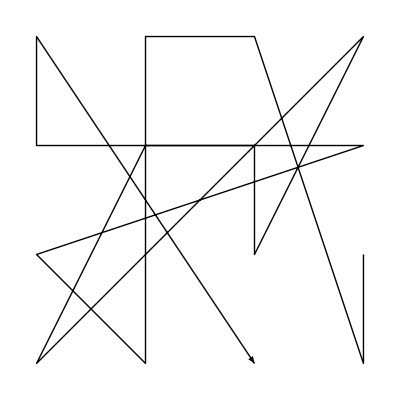
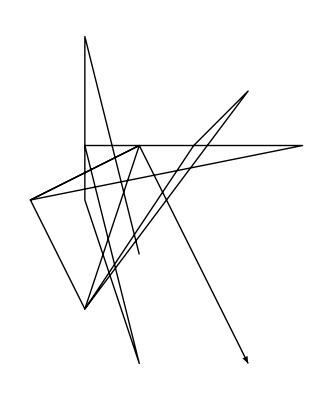
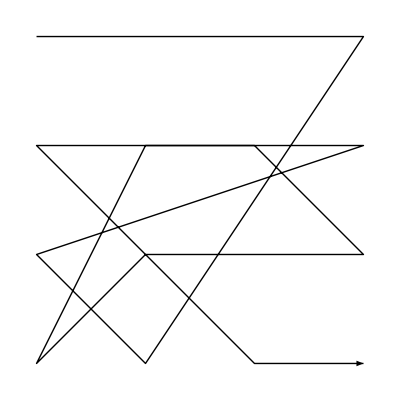
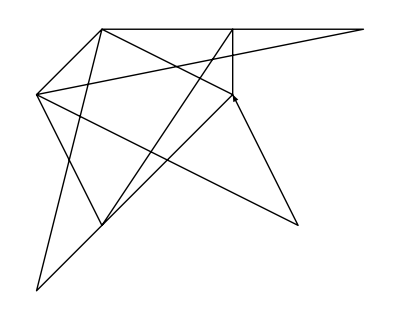
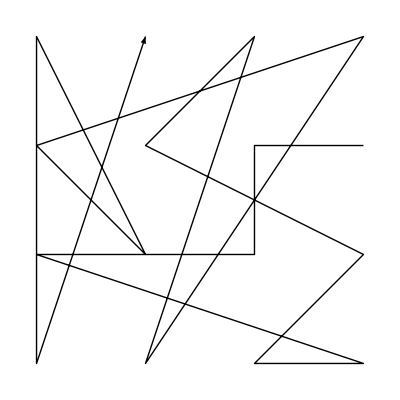
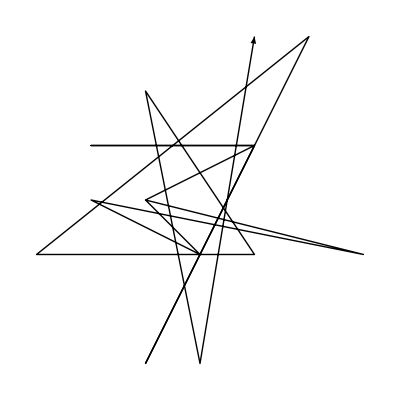
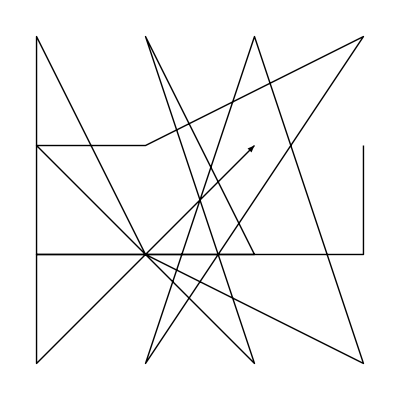
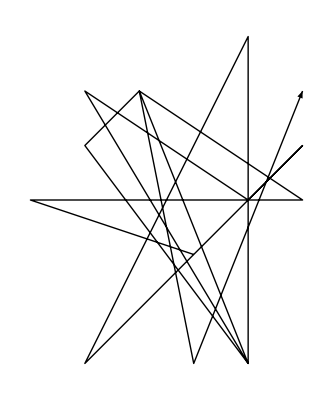
{{{(15 | 4 | 3 | 11
14 | 8 | 13 | 7
6 | 10 | 12 | 1
9 | 5 | 16 | 2),{-Graphics-,{{0,-1},{-1,3},{-1,0},{0,-3},{-1,1},{3,1},{-2,0},{-1,-2},{1,1},{2,2},{-1,-2},{0,1},{-2,0},{0,1},{2,-3}},-Graphics-}},{(1 | 2 | 3 | 4
14 | 8 | 13 | 7
6 | 10 | 11 | 12
9 | 5 | 15 | 16),{-Graphics-,{{1,0},{1,0},{1,0},{-2,-3},{-1,1},{3,1},{-2,0},{-1,-2},{1,1},{1,0},{1,0},{-1,1},{-2,0},{2,-2},{1,0}},-Graphics-}},Null},«43»,{{(14 | 16 | 9 | 11
12 | 8 | 2 | 1
4 | 13 | 3 | 7
15 | 10 | 6 | 5),{-Graphics-,{{-1,0},{0,-1},{-2,0},{3,-1},{-1,0},{1,1},{-2,1},{1,1},{-1,-3},{2,3},{-3,-1},{1,-1},{-1,2},{0,-3},{1,3}},-Graphics-}},{(14 | 5 | 11 | 9
7 | 8 | 16 | 1
3 | 13 | 4 | 2
15 | 10 | 6 | 12),{-Graphics-,{{0,-1},{-3,0},{2,0},{-1,2},{1,-3},{-2,2},{1,0},{2,1},{-2,-3},{1,3},{1,-3},{-2,1},{-1,2},{0,-3},{2,2}},-Graphics-}},Null}}

```mathematica
Map[{GM[Partition[Permute[Range[16],First[#]],4]],GM[Partition[Permute[Range[16],Last[#]],4]],}&,Out[155]]
```

```mathematica
Map[{{minters[Partition[Permute[Range[16],First[#]],4]],minters[Partition[Permute[Range[16],First[#]],4]]},{minters[Partition[Permute[Range[16],Last[#]],4]],minters[Partition[Permute[Range[16],Last[#]],4]]}}&,Out[155]]//Column
```

{{{52,{{15,4,3,11},{14,8,13,7},{6,10,12,1},{9,5,16,2}}},{52,{{15,4,3,11},{14,8,13,7},{6,10,12,1},{9,5,16,2}}}},{{52,{{1,2,3,4},{14,8,13,7},{6,10,11,12},{9,5,15,16}}},{52,{{1,2,3,4},{14,8,13,7},{6,10,11,12},{9,5,15,16}}}}}
{{{52,{{4,6,5,2},{7,8,1,10},{16,15,12,11},{9,14,13,3}}},{52,{{4,6,5,2},{7,8,1,10},{16,15,12,11},{9,14,13,3}}}},{{52,{{4,6,5,2},{7,8,1,10},{16,15,11,12},{9,14,13,3}}},{52,{{4,6,5,2},{7,8,1,10},{16,15,11,12},{9,14,13,3}}}}}
{{{52,{{7,10,16,14},{11,9,2,5},{1,6,3,4},{12,8,15,13}}},{52,{{7,10,16,14},{11,9,2,5},{1,6,3,4},{12,8,15,13}}}},{{52,{{1,2,8,16},{4,6,7,12},{9,10,14,3},{11,13,15,5}}},{52,{{1,2,8,16},{4,6,7,12},{9,10,14,3},{11,13,15,5}}}}}
{{{52,{{9,4,2,10},{13,11,1,12},{8,16,3,14},{7,6,5,15}}},{52,{{9,4,2,10},{13,11,1,12},{8,16,3,14},{7,6,5,15}}}},{{52,{{13,11,6,3},{16,12,5,1},{7,2,14,9},{15,8,10,4}}},{52,{{13,11,6,3},{16,12,5,1},{7,2,14,9},{15,8,10,4}}}}}
{{{52,{{6,12,1,2},{8,9,11,4},{3,14,5,16},{7,15,10,13}}},{52,{{6,12,1,2},{8,9,11,4},{3,14,5,16},{7,15,10,13}}}},{{52,{{9,16,6,12},{4,3,5,2},{1,15,8,13},{11,10,14,7}}},{52,{{9,16,6,12},{4,3,5,2},{1,15,8,13},{11,10,14,7}}}}}
{{{52,{{6,5,7,4},{13,11,16,9},{15,8,1,2},{10,14,3,12}}},{52,{{6,5,7,4},{13,11,16,9},{15,8,1,2},{10,14,3,12}}}},{{52,{{11,5,7,4},{13,1,16,9},{15,8,6,2},{10,14,3,12}}},{52,{{11,5,7,4},{13,1,16,9},{15,8,6,2},{10,14,3,12}}}}}
{{{52,{{5,10,15,7},{9,4,16,12},{2,13,8,3},{11,6,1,14}}},{52,{{5,10,15,7},{9,4,16,12},{2,13,8,3},{11,6,1,14}}}},{{52,{{13,12,2,14},{11,16,6,5},{8,3,1,9},{15,7,10,4}}},{52,{{13,12,2,14},{11,16,6,5},{8,3,1,9},{15,7,10,4}}}}}
{{{52,{{1,14,11,7},{16,9,10,13},{3,6,4,5},{2,15,12,8}}},{52,{{1,14,11,7},{16,9,10,13},{3,6,4,5},{2,15,12,8}}}},{{52,{{1,2,6,3},{5,7,11,8},{10,4,9,12},{13,14,15,16}}},{52,{{1,2,6,3},{5,7,11,8},{10,4,9,12},{13,14,15,16}}}}}
{{{52,{{7,1,6,9},{2,13,5,14},{11,12,4,3},{10,16,8,15}}},{52,{{7,1,6,9},{2,13,5,14},{11,12,4,3},{10,16,8,15}}}},{{52,{{1,2,12,11},{5,3,7,8},{4,13,9,10},{6,14,15,16}}},{52,{{1,2,12,11},{5,3,7,8},{4,13,9,10},{6,14,15,16}}}}}
{{{52,{{8,1,7,5},{13,10,11,15},{3,6,16,4},{14,2,12,9}}},{52,{{8,1,7,5},{13,10,11,15},{3,6,16,4},{14,2,12,9}}}},{{52,{{13,5,7,8},{15,10,11,14},{3,6,16,1},{12,4,2,9}}},{52,{{13,5,7,8},{15,10,11,14},{3,6,16,1},{12,4,2,9}}}}}
{{{52,{{8,3,16,9},{7,1,12,5},{10,6,13,4},{2,14,11,15}}},{52,{{8,3,16,9},{7,1,12,5},{10,6,13,4},{2,14,11,15}}}},{{52,{{12,11,13,1},{9,7,10,4},{8,5,16,6},{15,14,3,2}}},{52,{{12,11,13,1},{9,7,10,4},{8,5,16,6},{15,14,3,2}}}}}
{{{52,{{11,16,6,9},{2,1,7,3},{8,15,4,5},{13,12,10,14}}},{52,{{11,16,6,9},{2,1,7,3},{8,15,4,5},{13,12,10,14}}}},{{52,{{3,16,9,1},{2,8,7,4},{11,15,6,5},{13,12,10,14}}},{52,{{3,16,9,1},{2,8,7,4},{11,15,6,5},{13,12,10,14}}}}}
{{{52,{{12,14,4,9},{8,10,1,11},{15,16,13,2},{6,7,3,5}}},{52,{{12,14,4,9},{8,10,1,11},{15,16,13,2},{6,7,3,5}}}},{{52,{{1,2,4,9},{10,11,7,16},{15,13,5,12},{8,14,3,6}}},{52,{{1,2,4,9},{10,11,7,16},{15,13,5,12},{8,14,3,6}}}}}
{{{52,{{1,6,2,7},{16,15,14,12},{11,9,8,4},{10,13,5,3}}},{52,{{1,6,2,7},{16,15,14,12},{11,9,8,4},{10,13,5,3}}}},{{52,{{1,3,16,9},{15,2,11,13},{7,4,14,10},{12,8,6,5}}},{52,{{1,3,16,9},{15,2,11,13},{7,4,14,10},{12,8,6,5}}}}}
{{{52,{{3,14,9,2},{8,7,12,16},{4,13,10,5},{11,1,6,15}}},{52,{{3,14,9,2},{8,7,12,16},{4,13,10,5},{11,1,6,15}}}},{{52,{{9,1,4,14},{8,7,12,16},{2,11,13,5},{10,3,6,15}}},{52,{{9,1,4,14},{8,7,12,16},{2,11,13,5},{10,3,6,15}}}}}
{{{52,{{6,3,1,12},{11,16,5,15},{7,10,13,2},{8,9,14,4}}},{52,{{6,3,1,12},{11,16,5,15},{7,10,13,2},{8,9,14,4}}}},{{52,{{1,2,3,4},{7,6,9,13},{14,10,5,12},{11,15,8,16}}},{52,{{1,2,3,4},{7,6,9,13},{14,10,5,12},{11,15,8,16}}}}}
{{{52,{{4,9,2,3},{5,7,6,1},{10,16,14,15},{8,13,11,12}}},{52,{{4,9,2,3},{5,7,6,1},{10,16,14,15},{8,13,11,12}}}},{{52,{{4,9,2,3},{5,6,7,1},{10,16,14,15},{8,13,11,12}}},{52,{{4,9,2,3},{5,6,7,1},{10,16,14,15},{8,13,11,12}}}}}
{{{52,{{9,4,1,8},{16,14,5,2},{15,11,6,13},{10,12,7,3}}},{52,{{9,4,1,8},{16,14,5,2},{15,11,6,13},{10,12,7,3}}}},{{52,{{5,2,7,4},{9,13,1,8},{16,14,12,11},{6,10,3,15}}},{52,{{5,2,7,4},{9,13,1,8},{16,14,12,11},{6,10,3,15}}}}}
{{{52,{{1,2,16,13},{11,3,7,10},{5,6,15,12},{8,14,9,4}}},{52,{{1,2,16,13},{11,3,7,10},{5,6,15,12},{8,14,9,4}}}},{{52,{{1,2,10,3},{9,8,7,4},{15,13,5,12},{16,14,11,6}}},{52,{{1,2,10,3},{9,8,7,4},{15,13,5,12},{16,14,11,6}}}}}
{{{52,{{11,12,14,16},{2,13,1,3},{4,9,8,10},{15,7,6,5}}},{52,{{11,12,14,16},{2,13,1,3},{4,9,8,10},{15,7,6,5}}}},{{52,{{3,2,1,4},{5,6,8,7},{9,10,14,12},{13,11,15,16}}},{52,{{3,2,1,4},{5,6,8,7},{9,10,14,12},{13,11,15,16}}}}}
{{{52,{{7,2,1,10},{12,9,6,16},{11,5,8,15},{4,13,14,3}}},{52,{{7,2,1,10},{12,9,6,16},{11,5,8,15},{4,13,14,3}}}},{{52,{{16,2,8,13},{10,1,3,9},{7,4,6,5},{14,15,12,11}}},{52,{{16,2,8,13},{10,1,3,9},{7,4,6,5},{14,15,12,11}}}}}
{{{52,{{15,4,10,2},{1,6,3,16},{12,14,11,5},{7,13,8,9}}},{52,{{15,4,10,2},{1,6,3,16},{12,14,11,5},{7,13,8,9}}}},{{52,{{9,2,7,4},{16,6,13,5},{15,3,11,8},{14,10,12,1}}},{52,{{9,2,7,4},{16,6,13,5},{15,3,11,8},{14,10,12,1}}}}}
{{{52,{{10,2,4,3},{8,7,5,13},{12,15,14,16},{1,9,6,11}}},{52,{{10,2,4,3},{8,7,5,13},{12,15,14,16},{1,9,6,11}}}},{{52,{{7,2,3,4},{10,13,1,15},{14,5,16,9},{6,11,8,12}}},{52,{{7,2,3,4},{10,13,1,15},{14,5,16,9},{6,11,8,12}}}}}
{{{52,{{15,9,11,2},{12,10,6,13},{14,5,8,1},{16,4,7,3}}},{52,{{15,9,11,2},{12,10,6,13},{14,5,8,1},{16,4,7,3}}}},{{52,{{15,14,16,9},{12,10,6,11},{4,5,3,1},{8,2,7,13}}},{52,{{15,14,16,9},{12,10,6,11},{4,5,3,1},{8,2,7,13}}}}}
{{{52,{{1,14,16,8},{2,6,3,10},{9,13,7,4},{5,15,12,11}}},{52,{{1,14,16,8},{2,6,3,10},{9,13,7,4},{5,15,12,11}}}},{{52,{{1,5,7,12},{13,6,11,4},{9,8,16,15},{10,2,14,3}}},{52,{{1,5,7,12},{13,6,11,4},{9,8,16,15},{10,2,14,3}}}}}
{{{52,{{4,1,3,2},{7,13,5,6},{16,8,12,9},{15,14,11,10}}},{52,{{4,1,3,2},{7,13,5,6},{16,8,12,9},{15,14,11,10}}}},{{52,{{4,1,3,2},{5,13,7,6},{16,8,12,9},{15,14,11,10}}},{52,{{4,1,3,2},{5,13,7,6},{16,8,12,9},{15,14,11,10}}}}}
{{{52,{{10,14,16,7},{12,4,15,9},{1,6,2,3},{8,11,13,5}}},{52,{{10,14,16,7},{12,4,15,9},{1,6,2,3},{8,11,13,5}}}},{{52,{{7,14,12,8},{16,13,9,6},{4,15,2,5},{10,11,1,3}}},{52,{{7,14,12,8},{16,13,9,6},{4,15,2,5},{10,11,1,3}}}}}
{{{52,{{14,13,5,2},{8,4,10,9},{7,1,16,15},{12,11,6,3}}},{52,{{14,13,5,2},{8,4,10,9},{7,1,16,15},{12,11,6,3}}}},{{52,{{5,4,10,6},{1,15,16,14},{11,3,9,13},{2,8,12,7}}},{52,{{5,4,10,6},{1,15,16,14},{11,3,9,13},{2,8,12,7}}}}}
{{{52,{{8,3,9,6},{13,12,5,11},{10,2,15,7},{16,1,4,14}}},{52,{{8,3,9,6},{13,12,5,11},{10,2,15,7},{16,1,4,14}}}},{{52,{{5,2,3,1},{4,8,15,13},{9,10,16,11},{6,7,14,12}}},{52,{{5,2,3,1},{4,8,15,13},{9,10,16,11},{6,7,14,12}}}}}
{{{52,{{10,3,14,6},{8,15,9,7},{13,11,16,5},{2,12,1,4}}},{52,{{10,3,14,6},{8,15,9,7},{13,11,16,5},{2,12,1,4}}}},{{52,{{15,14,12,16},{7,4,13,9},{2,1,10,8},{3,5,6,11}}},{52,{{15,14,12,16},{7,4,13,9},{2,1,10,8},{3,5,6,11}}}}}
{{{52,{{11,8,6,10},{4,3,1,9},{16,13,15,12},{2,5,14,7}}},{52,{{11,8,6,10},{4,3,1,9},{16,13,15,12},{2,5,14,7}}}},{{52,{{4,1,3,9},{8,6,5,11},{15,16,10,12},{7,2,13,14}}},{52,{{4,1,3,9},{8,6,5,11},{15,16,10,12},{7,2,13,14}}}}}
{{{52,{{9,14,4,6},{3,1,2,10},{7,8,13,11},{12,15,5,16}}},{52,{{9,14,4,6},{3,1,2,10},{7,8,13,11},{12,15,5,16}}}},{{52,{{4,9,15,5},{14,3,1,8},{6,10,11,12},{13,7,2,16}}},{52,{{4,9,15,5},{14,3,1,8},{6,10,11,12},{13,7,2,16}}}}}
{{{52,{{10,7,14,5},{8,12,11,4},{13,15,16,6},{3,9,2,1}}},{52,{{10,7,14,5},{8,12,11,4},{13,15,16,6},{3,9,2,1}}}},{{52,{{10,7,13,5},{8,12,11,4},{14,15,16,6},{9,3,2,1}}},{52,{{10,7,13,5},{8,12,11,4},{14,15,16,6},{9,3,2,1}}}}}
{{{52,{{14,2,12,15},{10,16,5,11},{4,3,1,6},{9,13,8,7}}},{52,{{14,2,12,15},{10,16,5,11},{4,3,1,6},{9,13,8,7}}}},{{52,{{4,2,5,1},{16,3,6,13},{11,7,9,10},{8,15,14,12}}},{52,{{4,2,5,1},{16,3,6,13},{11,7,9,10},{8,15,14,12}}}}}
{{{52,{{14,13,10,7},{9,8,16,4},{5,1,3,2},{11,15,12,6}}},{52,{{14,13,10,7},{9,8,16,4},{5,1,3,2},{11,15,12,6}}}},{{52,{{10,12,11,4},{9,6,7,8},{5,3,13,15},{2,1,14,16}}},{52,{{10,12,11,4},{9,6,7,8},{5,3,13,15},{2,1,14,16}}}}}
{{{52,{{10,12,4,3},{5,15,9,13},{6,14,7,2},{1,16,11,8}}},{52,{{10,12,4,3},{5,15,9,13},{6,14,7,2},{1,16,11,8}}}},{{52,{{16,12,4,3},{5,15,9,10},{6,8,7,2},{14,13,11,1}}},{52,{{16,12,4,3},{5,15,9,10},{6,8,7,2},{14,13,11,1}}}}}
{{{52,{{3,7,13,11},{2,5,10,12},{4,9,15,8},{6,14,16,1}}},{52,{{3,7,13,11},{2,5,10,12},{4,9,15,8},{6,14,16,1}}}},{{52,{{3,7,13,11},{2,5,10,8},{4,9,15,12},{6,14,16,1}}},{52,{{3,7,13,11},{2,5,10,8},{4,9,15,12},{6,14,16,1}}}}}
{{{52,{{9,16,7,10},{15,1,11,14},{2,8,4,5},{3,6,12,13}}},{52,{{9,16,7,10},{15,1,11,14},{2,8,4,5},{3,6,12,13}}}},{{52,{{10,14,9,13},{12,4,2,7},{8,3,16,15},{1,11,5,6}}},{52,{{10,14,9,13},{12,4,2,7},{8,3,16,15},{1,11,5,6}}}}}
{{{52,{{2,14,9,13},{16,12,3,4},{5,7,6,8},{1,10,11,15}}},{52,{{2,14,9,13},{16,12,3,4},{5,7,6,8},{1,10,11,15}}}},{{52,{{11,6,13,16},{2,3,4,5},{1,8,7,9},{15,12,10,14}}},{52,{{11,6,13,16},{2,3,4,5},{1,8,7,9},{15,12,10,14}}}}}
{{{52,{{3,7,10,9},{8,14,13,11},{2,5,1,4},{12,15,16,6}}},{52,{{3,7,10,9},{8,14,13,11},{2,5,1,4},{12,15,16,6}}}},{{52,{{8,4,11,13},{3,6,9,10},{12,1,5,7},{2,14,15,16}}},{52,{{8,4,11,13},{3,6,9,10},{12,1,5,7},{2,14,15,16}}}}}
{{{52,{{11,8,1,10},{5,4,12,2},{15,13,16,9},{7,6,14,3}}},{52,{{11,8,1,10},{5,4,12,2},{15,13,16,9},{7,6,14,3}}}},{{52,{{3,8,16,14},{5,15,10,2},{7,6,1,13},{4,9,12,11}}},{52,{{3,8,16,14},{5,15,10,2},{7,6,1,13},{4,9,12,11}}}}}
{{{52,{{14,7,10,4},{12,1,6,9},{15,13,16,2},{3,5,11,8}}},{52,{{14,7,10,4},{12,1,6,9},{15,13,16,2},{3,5,11,8}}}},{{52,{{7,5,3,4},{1,2,12,9},{15,10,16,14},{13,6,11,8}}},{52,{{7,5,3,4},{1,2,12,9},{15,10,16,14},{13,6,11,8}}}}}
{{{52,{{6,12,10,11},{7,14,1,15},{8,9,3,5},{16,13,4,2}}},{52,{{6,12,10,11},{7,14,1,15},{8,9,3,5},{16,13,4,2}}}},{{52,{{16,1,3,4},{14,2,13,8},{9,10,11,6},{5,12,15,7}}},{52,{{16,1,3,4},{14,2,13,8},{9,10,11,6},{5,12,15,7}}}}}
{{{52,{{1,13,2,16},{5,10,6,14},{3,8,4,9},{12,11,15,7}}},{52,{{1,13,2,16},{5,10,6,14},{3,8,4,9},{12,11,15,7}}}},{{52,{{1,12,13,10},{5,11,14,16},{2,4,6,3},{9,7,15,8}}},{52,{{1,12,13,10},{5,11,14,16},{2,4,6,3},{9,7,15,8}}}}}
{{{52,{{14,16,9,11},{12,8,2,1},{4,13,3,7},{15,10,6,5}}},{52,{{14,16,9,11},{12,8,2,1},{4,13,3,7},{15,10,6,5}}}},{{52,{{14,5,11,9},{7,8,16,1},{3,13,4,2},{15,10,6,12}}},{52,{{14,5,11,9},{7,8,16,1},{3,13,4,2},{15,10,6,12}}}}}

```mathematica
Table[Out[155][[i]],{i,{9,16,17,25,36}}]
```

{{Cycles[{{1,2,5,7},{3,12,10,13,6},{4,11,9},{8,15,16,14}}],Cycles[{{3,6,13,10,12},{4,9,11}}]},{Cycles[{{1,3,2,12,4,16,6},{5,7,9,14,15,8,13,11}}],Cycles[{{5,11,13,8,15,14,9,7}}]},{Cycles[{{1,8,13,14,11,15,12,16,10,9,2,3,4},{6,7}}],Cycles[{{1,8,13,14,11,15,12,16,10,9,2,3,4}}]},{Cycles[{{2,5,13,10,8,4,12,15,14},{3,7,11,16}}],Cycles[{{2,14,15,12,4,8,10,13,5},{3,16,11,7}}]},{Cycles[{{1,13,8,16,14,10},{2,12},{3,4},{6,9,7,11,15}}],Cycles[{{1,16},{2,12},{3,4},{6,9,7,11,15},{8,10},{13,14}}]}}

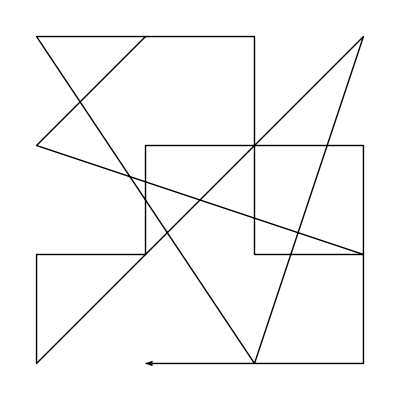
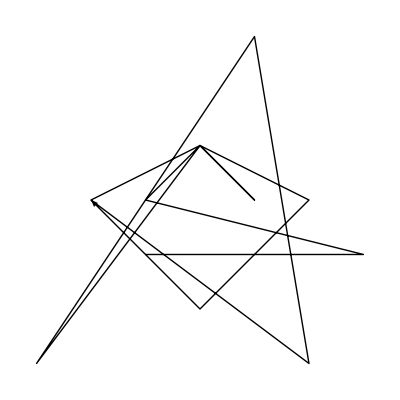
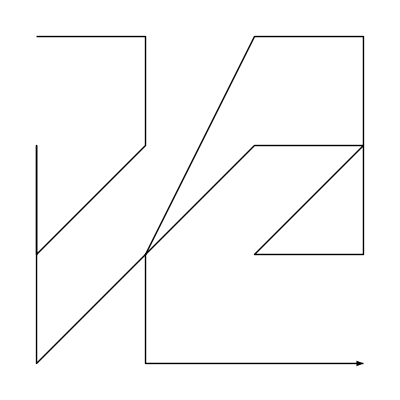
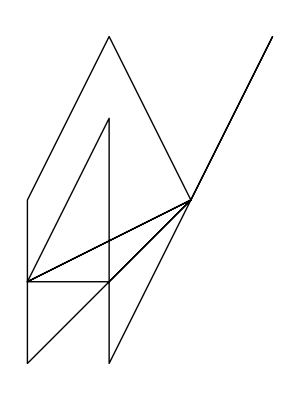
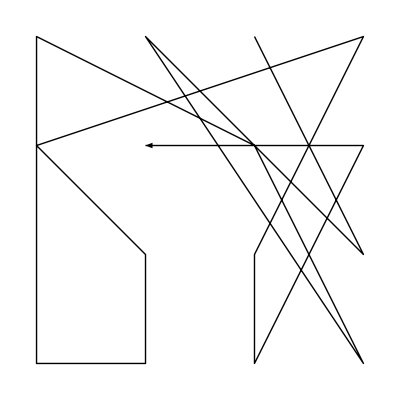
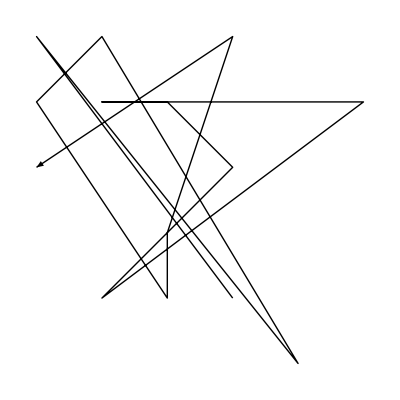
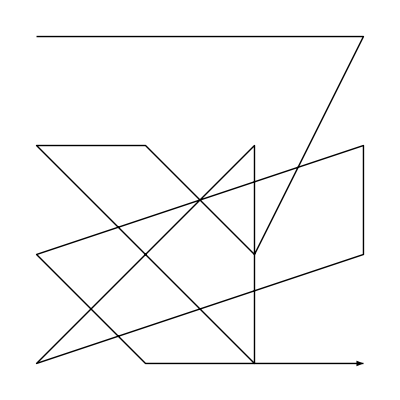
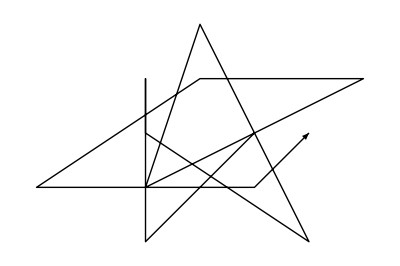
{{(7 | 1 | 6 | 9
2 | 13 | 5 | 14
11 | 12 | 4 | 3
10 | 16 | 8 | 15),{-Graphics-,{{-1,-1},{3,-1},{-1,0},{0,1},{0,1},{-2,0},{2,-3},{1,3},{-3,-3},{0,1},{1,0},{0,1},{2,0},{0,-2},{-2,0}},-Graphics-}},{(1 | 2 | 12 | 11
5 | 3 | 7 | 8
4 | 13 | 9 | 10
6 | 14 | 15 | 16),{-Graphics-,{{1,0},{0,-1},{-1,-1},{0,1},{0,-2},{2,2},{1,0},{-1,-1},{1,0},{0,2},{-1,0},{-1,-2},{0,-1},{1,0},{1,0}},-Graphics-}},Null,(□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □)}
{{(6 | 3 | 1 | 12
11 | 16 | 5 | 15
7 | 10 | 13 | 2
8 | 9 | 14 | 4),{-Graphics-,{{1,-2},{-2,2},{2,-3},{-1,2},{-2,1},{0,-2},{0,-1},{1,0},{0,1},{-1,1},{3,1},{-1,-2},{0,-1},{1,2},{-2,0}},-Graphics-}},{(1 | 2 | 3 | 4
7 | 6 | 9 | 13
14 | 10 | 5 | 12
11 | 15 | 8 | 16),{-Graphics-,{{1,0},{1,0},{1,0},{-1,-2},{-1,1},{-1,0},{2,-2},{0,2},{-1,-1},{-1,-1},{3,1},{0,1},{-3,-1},{1,-1},{2,0}},-Graphics-}},Null,(□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □)}
{{(4 | 9 | 2 | 3
5 | 7 | 6 | 1
10 | 16 | 14 | 15
8 | 13 | 11 | 12),{-Graphics-,{{-1,1},{1,0},{-3,0},{0,-1},{2,0},{-1,0},{-1,-2},{1,3},{-1,-2},{2,-1},{1,0},{-2,0},{1,1},{1,0},{-2,0}},-Graphics-}},{(4 | 9 | 2 | 3
5 | 6 | 7 | 1
10 | 16 | 14 | 15
8 | 13 | 11 | 12),{-Graphics-,{{-1,1},{1,0},{-3,0},{0,-1},{1,0},{1,0},{-2,-2},{1,3},{-1,-2},{2,-1},{1,0},{-2,0},{1,1},{1,0},{-2,0}},-Graphics-}},Null,(□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □)}
{{(1 | 14 | 16 | 8
2 | 6 | 3 | 10
9 | 13 | 7 | 4
5 | 15 | 12 | 11),{-Graphics-,{{0,-1},{2,0},{1,-1},{-3,-1},{1,2},{1,-1},{1,2},{-3,-2},{3,1},{0,-2},{-1,0},{-1,1},{0,2},{0,-3},{1,3}},-Graphics-}},{(1 | 5 | 7 | 12
13 | 6 | 11 | 4
9 | 8 | 16 | 15
10 | 2 | 14 | 3),{-Graphics-,{{1,-3},{2,0},{0,2},{-2,1},{0,-1},{1,1},{-1,-2},{-1,0},{0,-1},{2,2},{1,1},{-3,-1},{2,-2},{1,1},{-1,0}},-Graphics-}},Null,(□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □)}
{{(10 | 12 | 4 | 3
5 | 15 | 9 | 13
6 | 14 | 7 | 2
1 | 16 | 11 | 8),{-Graphics-,{{3,1},{0,2},{-1,0},{-2,-1},{0,-1},{2,0},{1,-1},{-1,2},{-2,1},{2,-3},{-1,3},{2,-1},{-2,-1},{0,1},{0,-2}},-Graphics-}},{(16 | 12 | 4 | 3
5 | 15 | 9 | 10
6 | 8 | 7 | 2
14 | 13 | 11 | 1),{-Graphics-,{{0,1},{0,2},{-1,0},{-2,-1},{0,-1},{2,0},{-1,0},{1,1},{1,0},{-1,-2},{-1,3},{0,-3},{-1,0},{1,2},{-1,1}},-Graphics-}},Null,(□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □)}

```mathematica
Table[Join[Out[243][[i]],{MatrixForm[({{□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}})]}],{i,{9,16,17,25,36}}]//Column
```

```mathematica
14,66,36,30,14
5,3,9,3,5
```

```mathematica
Map[{{mat2perord[Partition[Permute[Range[16],First[#]],4]],mat2perord[Partition[Permute[Range[16],First[#]],4]]},{mat2perord[Partition[Permute[Range[16],Last[#]],4]],mat2perord[Partition[Permute[Range[16],Last[#]],4]]}}&,Out[155]]//Column
```

{{12,12},{42,42}}
{{28,28},{36,36}}
{{56,56},{30,30}}
{{12,12},{14,14}}
{{60,60},{14,14}}
{{105,105},{9,9}}
{{13,13},{36,36}}
{{10,10},{6,6}}
{{14,14},{14,14}}
{{18,18},{12,12}}
{{66,66},{10,10}}
{{66,66},{12,12}}
{{14,14},{12,12}}
{{26,26},{16,16}}
{{22,22},{12,12}}
{{66,66},{66,66}}
{{36,36},{36,36}}
{{26,26},{30,30}}
{{30,30},{18,18}}
{{14,14},{4,4}}
{{20,20},{55,55}}
{{140,140},{15,15}}
{{15,15},{12,12}}
{{14,14},{9,9}}
{{30,30},{30,30}}
{{12,12},{105,105}}
{{26,26},{56,56}}
{{39,39},{30,30}}
{{15,15},{30,30}}
{{15,15},{30,30}}
{{36,36},{13,13}}
{{36,36},{6,6}}
{{39,39},{14,14}}
{{16,16},{28,28}}
{{14,14},{6,6}}
{{36,36},{42,42}}
{{14,14},{14,14}}
{{60,60},{15,15}}
{{40,40},{39,39}}
{{12,12},{39,39}}
{{39,39},{63,63}}
{{36,36},{63,63}}
{{22,22},{6,6}}
{{56,56},{12,12}}
{{20,20},{16,16}}

```mathematica
10000000/16056.72
```

622.792

```mathematica
RandomPermutation[9]
```

```mathematica
DeleteCases[Cycles[{{1,7,8,2,6,5,9,3}}],]
```

```mathematica
PermutationOrder[Cycles[{{1,7,8,2,6,5,9,3}}]]
```

8

```mathematica
mat42ran[range_]:=Do[Print[j];Do[Block[{mat=Partition[Permute[Range[16],RandomPermutation[16]],4]},Block[{d=Abs[Det[mat]]},Piecewise[{{0,d>1},{mat>>>"mat42.log",d<2}}]]],{i,j,j+1000}],{j,1,range,1000}]
```

```mathematica
mat42ran[10000]
```

1

1001

2001

3001

4001

5001

6001

7001

8001

9001

```mathematica
PartitionsP[16]
```

231

```mathematica
Sort[Map[{Apply[LCM,#],#}&,IntegerPartitions[16]],First[#1]>First[#2]&]
```

{{140,{7,5,4}},{120,{8,5,3}},{105,{7,5,3,1}},{90,{9,5,2}},{84,{7,4,3,1,1}},{84,{7,4,3,2}},{70,{7,5,2,1,1}},{70,{7,5,2,2}},{66,{11,3,2}},{63,{9,7}},{60,{5,4,3,1,1,1,1}},{60,{5,4,3,2,1,1}},{60,{5,4,3,2,2}},{60,{5,4,3,3,1}},{60,{5,4,4,3}},{60,{6,5,4,1}},{56,{8,7,1}},{55,{11,5}},{45,{9,5,1,1}},{44,{11,4,1}},{42,{7,3,2,1,1,1,1}},{42,{7,3,2,2,1,1}},{42,{7,3,2,2,2}},{42,{7,3,3,2,1}},{42,{7,6,1,1,1}},{42,{7,6,2,1}},{42,{7,6,3}},{40,{8,5,1,1,1}},{40,{8,5,2,1}},{39,{13,3}},{36,{9,4,1,1,1}},{36,{9,4,2,1}},{36,{9,4,3}},{35,{7,5,1,1,1,1}},{33,{11,3,1,1}},{30,{5,3,2,1,1,1,1,1,1}},{30,{5,3,2,2,1,1,1,1}},{30,{5,3,2,2,2,1,1}},{30,{5,3,2,2,2,2}},{30,{5,3,3,2,1,1,1}},{30,{5,3,3,2,2,1}},{30,{5,3,3,3,2}},{30,{5,5,3,2,1}},{30,{6,5,1,1,1,1,1}},{30,{6,5,2,1,1,1}},{30,{6,5,2,2,1}},{30,{6,5,3,1,1}},{30,{6,5,3,2}},{30,{6,5,5}},{30,{10,3,1,1,1}},{30,{10,3,2,1}},{30,{10,3,3}},{30,{10,6}},{28,{7,4,1,1,1,1,1}},{28,{7,4,2,1,1,1}},{28,{7,4,2,2,1}},{28,{7,4,4,1}},{26,{13,2,1}},{24,{8,3,1,1,1,1,1}},{24,{8,3,2,1,1,1}},{24,{8,3,2,2,1}},{24,{8,3,3,1,1}},{24,{8,3,3,2}},{24,{8,4,3,1}},{24,{8,6,1,1}},{24,{8,6,2}},{22,{11,2,1,1,1}},{22,{11,2,2,1}},{21,{7,3,1,1,1,1,1,1}},{21,{7,3,3,1,1,1}},{21,{7,3,3,3}},{20,{5,4,1,1,1,1,1,1,1}},{20,{5,4,2,1,1,1,1,1}},{20,{5,4,2,2,1,1,1}},{20,{5,4,2,2,2,1}},{20,{5,4,4,1,1,1}},{20,{5,4,4,2,1}},{20,{5,5,4,1,1}},{20,{5,5,4,2}},{20,{10,4,1,1}},{20,{10,4,2}},{18,{9,2,1,1,1,1,1}},{18,{9,2,2,1,1,1}},{18,{9,2,2,2,1}},{18,{9,3,2,1,1}},{18,{9,3,2,2}},{18,{9,6,1}},{16,{16}},{15,{5,3,1,1,1,1,1,1,1,1}},{15,{5,3,3,1,1,1,1,1}},{15,{5,3,3,3,1,1}},{15,{5,5,3,1,1,1}},{15,{5,5,3,3}},{15,{15,1}},{14,{7,2,1,1,1,1,1,1,1}},{14,{7,2,2,1,1,1,1,1}},{14,{7,2,2,2,1,1,1}},{14,{7,2,2,2,2,1}},{14,{7,7,2}},{14,{14,1,1}},{14,{14,2}},{13,{13,1,1,1}},{12,{4,3,1,1,1,1,1,1,1,1,1}},{12,{4,3,2,1,1,1,1,1,1,1}},{12,{4,3,2,2,1,1,1,1,1}},{12,{4,3,2,2,2,1,1,1}},{12,{4,3,2,2,2,2,1}},{12,{4,3,3,1,1,1,1,1,1}},{12,{4,3,3,2,1,1,1,1}},{12,{4,3,3,2,2,1,1}},{12,{4,3,3,2,2,2}},{12,{4,3,3,3,1,1,1}},{12,{4,3,3,3,2,1}},{12,{4,3,3,3,3}},{12,{4,4,3,1,1,1,1,1}},{12,{4,4,3,2,1,1,1}},{12,{4,4,3,2,2,1}},{12,{4,4,3,3,1,1}},{12,{4,4,3,3,2}},{12,{4,4,4,3,1}},{12,{6,4,1,1,1,1,1,1}},{12,{6,4,2,1,1,1,1}},{12,{6,4,2,2,1,1}},{12,{6,4,2,2,2}},{12,{6,4,3,1,1,1}},{12,{6,4,3,2,1}},{12,{6,4,3,3}},{12,{6,4,4,1,1}},{12,{6,4,4,2}},{12,{6,6,4}},{12,{12,1,1,1,1}},{12,{12,2,1,1}},{12,{12,2,2}},{12,{12,3,1}},{12,{12,4}},{11,{11,1,1,1,1,1}},{10,{5,2,1,1,1,1,1,1,1,1,1}},{10,{5,2,2,1,1,1,1,1,1,1}},{10,{5,2,2,2,1,1,1,1,1}},{10,{5,2,2,2,2,1,1,1}},{10,{5,2,2,2,2,2,1}},{10,{5,5,2,1,1,1,1}},{10,{5,5,2,2,1,1}},{10,{5,5,2,2,2}},{10,{10,1,1,1,1,1,1}},{10,{10,2,1,1,1,1}},{10,{10,2,2,1,1}},{10,{10,2,2,2}},{10,{10,5,1}},{9,{9,1,1,1,1,1,1,1}},{9,{9,3,1,1,1,1}},{9,{9,3,3,1}},{8,{8,1,1,1,1,1,1,1,1}},{8,{8,2,1,1,1,1,1,1}},{8,{8,2,2,1,1,1,1}},{8,{8,2,2,2,1,1}},{8,{8,2,2,2,2}},{8,{8,4,1,1,1,1}},{8,{8,4,2,1,1}},{8,{8,4,2,2}},{8,{8,4,4}},{8,{8,8}},{7,{7,1,1,1,1,1,1,1,1,1}},{7,{7,7,1,1}},{6,{3,2,1,1,1,1,1,1,1,1,1,1,1}},{6,{3,2,2,1,1,1,1,1,1,1,1,1}},{6,{3,2,2,2,1,1,1,1,1,1,1}},{6,{3,2,2,2,2,1,1,1,1,1}},{6,{3,2,2,2,2,2,1,1,1}},{6,{3,2,2,2,2,2,2,1}},{6,{3,3,2,1,1,1,1,1,1,1,1}},{6,{3,3,2,2,1,1,1,1,1,1}},{6,{3,3,2,2,2,1,1,1,1}},{6,{3,3,2,2,2,2,1,1}},{6,{3,3,2,2,2,2,2}},{6,{3,3,3,2,1,1,1,1,1}},{6,{3,3,3,2,2,1,1,1}},{6,{3,3,3,2,2,2,1}},{6,{3,3,3,3,2,1,1}},{6,{3,3,3,3,2,2}},{6,{6,1,1,1,1,1,1,1,1,1,1}},{6,{6,2,1,1,1,1,1,1,1,1}},{6,{6,2,2,1,1,1,1,1,1}},{6,{6,2,2,2,1,1,1,1}},{6,{6,2,2,2,2,1,1}},{6,{6,2,2,2,2,2}},{6,{6,3,1,1,1,1,1,1,1}},{6,{6,3,2,1,1,1,1,1}},{6,{6,3,2,2,1,1,1}},{6,{6,3,2,2,2,1}},{6,{6,3,3,1,1,1,1}},{6,{6,3,3,2,1,1}},{6,{6,3,3,2,2}},{6,{6,3,3,3,1}},{6,{6,6,1,1,1,1}},{6,{6,6,2,1,1}},{6,{6,6,2,2}},{6,{6,6,3,1}},{5,{5,1,1,1,1,1,1,1,1,1,1,1}},{5,{5,5,1,1,1,1,1,1}},{5,{5,5,5,1}},{4,{4,1,1,1,1,1,1,1,1,1,1,1,1}},{4,{4,2,1,1,1,1,1,1,1,1,1,1}},{4,{4,2,2,1,1,1,1,1,1,1,1}},{4,{4,2,2,2,1,1,1,1,1,1}},{4,{4,2,2,2,2,1,1,1,1}},{4,{4,2,2,2,2,2,1,1}},{4,{4,2,2,2,2,2,2}},{4,{4,4,1,1,1,1,1,1,1,1}},{4,{4,4,2,1,1,1,1,1,1}},{4,{4,4,2,2,1,1,1,1}},{4,{4,4,2,2,2,1,1}},{4,{4,4,2,2,2,2}},{4,{4,4,4,1,1,1,1}},{4,{4,4,4,2,1,1}},{4,{4,4,4,2,2}},{4,{4,4,4,4}},{3,{3,1,1,1,1,1,1,1,1,1,1,1,1,1}},{3,{3,3,1,1,1,1,1,1,1,1,1,1}},{3,{3,3,3,1,1,1,1,1,1,1}},{3,{3,3,3,3,1,1,1,1}},{3,{3,3,3,3,3,1}},{2,{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{2,{2,2,1,1,1,1,1,1,1,1,1,1,1,1}},{2,{2,2,2,1,1,1,1,1,1,1,1,1,1}},{2,{2,2,2,2,1,1,1,1,1,1,1,1}},{2,{2,2,2,2,2,1,1,1,1,1,1}},{2,{2,2,2,2,2,2,1,1,1,1}},{2,{2,2,2,2,2,2,2,1,1}},{2,{2,2,2,2,2,2,2,2}},{1,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
16 15 14 13 12 11 10
```

57657600

```mathematica
Subsets[Range[16],{7}]
```

{{1,2,3,4,5,6,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,6,10},{1,2,3,4,5,6,11},{1,2,3,4,5,6,12},{1,2,3,4,5,6,13},{1,2,3,4,5,6,14},{1,2,3,4,5,6,15},{1,2,3,4,5,6,16},{1,2,3,4,5,7,8},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,7,11},{1,2,3,4,5,7,12},{1,2,3,4,5,7,13},{1,2,3,4,5,7,14},{1,2,3,4,5,7,15},{1,2,3,4,5,7,16},{1,2,3,4,5,8,9},{1,2,3,4,5,8,10},«11399»,{8,9,11,12,13,14,16},{8,9,11,12,13,15,16},{8,9,11,12,14,15,16},{8,9,11,13,14,15,16},{8,9,12,13,14,15,16},{8,10,11,12,13,14,15},{8,10,11,12,13,14,16},{8,10,11,12,13,15,16},{8,10,11,12,14,15,16},{8,10,11,13,14,15,16},{8,10,12,13,14,15,16},{8,11,12,13,14,15,16},{9,10,11,12,13,14,15},{9,10,11,12,13,14,16},{9,10,11,12,13,15,16},{9,10,11,12,14,15,16},{9,10,11,13,14,15,16},{9,10,12,13,14,15,16},{9,11,12,13,14,15,16},{10,11,12,13,14,15,16}}

```mathematica
Map[Cycles[{#,Take[Complement[Range[16],#],4],Take[Complement[Range[16],#],-5]}]&,%]
```

{Cycles[{{1,2,3,4,5,6,7},{8,9,10,11},{12,13,14,15,16}}],Cycles[{{1,2,3,4,5,6,8},{7,9,10,11},{12,13,14,15,16}}],Cycles[{{1,2,3,4,5,6,9},{7,8,10,11},{12,13,14,15,16}}],Cycles[{{1,2,3,4,5,6,10},{7,8,9,11},{12,13,14,15,16}}],Cycles[{{1,2,3,4,5,6,11},{7,8,9,10},{12,13,14,15,16}}],Cycles[{{1,2,3,4,5,6,12},{7,8,9,10},{11,13,14,15,16}}],Cycles[{{1,2,3,4,5,6,13},{7,8,9,10},{11,12,14,15,16}}],«11426»,Cycles[{{1,2,3,4},{5,6,7,8,15},{9,10,11,12,13,14,16}}],Cycles[{{1,2,3,4},{5,6,7,8,14},{9,10,11,12,13,15,16}}],Cycles[{{1,2,3,4},{5,6,7,8,13},{9,10,11,12,14,15,16}}],Cycles[{{1,2,3,4},{5,6,7,8,12},{9,10,11,13,14,15,16}}],Cycles[{{1,2,3,4},{5,6,7,8,11},{9,10,12,13,14,15,16}}],Cycles[{{1,2,3,4},{5,6,7,8,10},{9,11,12,13,14,15,16}}],Cycles[{{1,2,3,4},{5,6,7,8,9},{10,11,12,13,14,15,16}}]}

```mathematica
Length[Out[182]]
```

11440

```mathematica
Timing[Monitor[Table[wch[Out[182][[i]]],{i,1,11440}],i]]
```

{107.82,{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},«11294»,{},{},{},{Cycles[{{1,3},{2,4},{5,16,10,9,6},{7,8,11,12,13,14,15}}]},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{Cycles[{{5,13,12,8,6},{7,14,9,15,10,16,11}}],Cycles[{{1,4,3,2},{7,16,15,14,11,10,9}}]},{},{},{},{},{Cycles[{{1,3},{2,4},{5,6,8,11,12},{7,15,13,9,16,14,10}}],Cycles[{{1,4,3,2},{5,8,12,6,11},{7,15,13,9,16,14,10}}]},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{Cycles[{{8,16,15,12,11,10,9}}]},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{Cycles[{{1,3},{2,4},{5,6,7,8,11},{9,10,12,13,14,15,16}}]},{},{}}}

```mathematica
Last[Out[184]]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},«11286»,{},{},{},{},{},{},{},{Cycles[{{1,3},{2,4},{5,16,10,9,6},{7,8,11,12,13,14,15}}]},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{Cycles[{{5,13,12,8,6},{7,14,9,15,10,16,11}}],Cycles[{{1,4,3,2},{7,16,15,14,11,10,9}}]},{},{},{},{},{Cycles[{{1,3},{2,4},{5,6,8,11,12},{7,15,13,9,16,14,10}}],Cycles[{{1,4,3,2},{5,8,12,6,11},{7,15,13,9,16,14,10}}]},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{Cycles[{{8,16,15,12,11,10,9}}]},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{Cycles[{{1,3},{2,4},{5,6,7,8,11},{9,10,12,13,14,15,16}}]},{},{}}

```mathematica
DeleteCases[%,{}]
```

{{Cycles[{{5,9,8,6},{10,14,12,15,13}}]},{Cycles[{{1,14,10,8,4,3,2},{11,15,12,16,13}}]},{Cycles[{{5,8,7,6},{11,13,16,12,14}}]},{Cycles[{{1,3,11,16,2,4,12},{5,7},{6,8},{9,15,14,13,10}}]},{Cycles[{{1,13,4,2,14,12,3},{5,6,7,8},{9,10,11,15,16}}]},{Cycles[{{4,9},{8,10},{12,16,15,14,13}}]},{Cycles[{{4,9,8,6},{10,14,16,12,15}}]},{Cycles[{{4,9,8,6},{10,11,12,13,15}}]},{Cycles[{{1,2,3,5,8,12,15},{4,9,7,6},{10,14,11,16,13}}]},{Cycles[{{1,15,11,7,6,3,2},{10,16,14,13,12}}]},{Cycles[{{1,14,11,10,6,3,2},{9,15,12,16,13}}]},{Cycles[{{1,2,3,7,8,12,15},{4,6},{5,9}}]},{Cycles[{{1,2,3,7,9,12,16},{4,8,6,5},{10,11,13,14,15}}]},{Cycles[{{1,13,2,14,3,16,7},{4,5,6,8},{9,11,15,10,12}}]},{Cycles[{{4,5,6,7},{10,12,13,14,16}}],Cycles[{{1,15,11,9,8,3,2},{4,6},{5,7},{10,14,12,16,13}}]},{Cycles[{{4,5,6,7},{10,13,15,11,14}}]},{Cycles[{{4,5,6,7},{10,14,11,15,12}}]},{Cycles[{{1,16,12,10,9,3,2},{4,5,6,7}}]},{Cycles[{{1,13,9,2,16,11,3},{8,14,10,15,12}}]},{Cycles[{{1,11,16,3,15,2,12},{4,7,6,5},{8,13,9,14,10}}]},{Cycles[{{3,8,9,10},{11,13,15,12,14}}]},{Cycles[{{3,7,9,10},{11,13,14,15,16}}]},{Cycles[{{1,16,10,7,5,4,2},{3,8},{6,9}}]},{Cycles[{{1,2,4,5,7,11,12},{3,9,8,6}}]},{Cycles[{{1,5,15,4,11,2,7},{3,9,8,6},{10,13,16,12,14}}]},{Cycles[{{1,5,15,4,10,2,9},{3,6,7,8}}]},{Cycles[{{1,12,9,8,6,4,2},{11,16,15,14,13}}]},{Cycles[{{1,13,6,2,14,9,4},{3,5,7,8},{10,15,11,16,12}}]},{Cycles[{{1,4,8,10,2,7,9},{12,13,14,15,16}}]},{Cycles[{{3,5,6,9},{11,13,16,12,15}}]},{Cycles[{{1,2,4,9,10,11,13},{3,7,6,5},{8,14,16,12,15}}]},{Cycles[{{3,7,6,5},{8,11,13,14,15}}]},{Cycles[{{1,13,10,2,15,11,4},{3,5,6,7}}]},{Cycles[{{1,16,15,13,10,4,2},{3,5,6,7},{8,14,12,11,9}}]},{Cycles[{{1,16,15,13,11,4,2},{3,6},{5,7}}]},{Cycles[{{1,16,15,13,12,4,2},{3,5,6,7},{8,14,11,10,9}}]},{Cycles[{{1,2,5,6,7,8,9}}]},{Cycles[{{1,7,2,13,5,14,6},{3,9,8,4},{10,12,16,11,15}}]},{Cycles[{{1,16,10,8,7,5,2},{3,6},{4,9},{11,14,12,15,13}}]},{Cycles[{{3,7,6,4},{8,13,16,10,15}}]},{Cycles[{{1,15,12,11,10,5,2},{8,9,13,14,16}}]},{Cycles[{{1,12,7,2,16,10,6},{3,8,5,4},{9,13,15,11,14}}]},{Cycles[{{3,7,5,4},{10,15,14,13,12}}]},{Cycles[{{3,7,5,4},{9,16,12,11,10}}]},{Cycles[{{3,5},{4,7},{8,9,10,12,16}}]},{Cycles[{{1,14,12,11,8,7,2},{9,13,16,10,15}}]},{Cycles[{{1,7,11,16,2,8,14},{3,5},{4,6},{9,12,15,10,13}}]},{Cycles[{{1,11,9,2,12,10,7},{3,5},{4,6},{8,15,13,16,14}}]},{Cycles[{{1,9,14,7,11,2,10},{3,5},{4,6},{8,12,13,15,16}}]},{Cycles[{{3,4,5,6},{7,8,10,11,14}}]},{Cycles[{{1,13,2,14,10,16,11},{3,4,5,6},{7,15,12,9,8}}]},{Cycles[{{1,5,10,4,9,3,6},{2,11,8,7}}]},{Cycles[{{1,3,4,5,8,12,13},{2,6,7,9},{10,16,15,14,11}}]},{Cycles[{{1,12,11,7,6,4,3},{10,16,15,14,13}}]},{Cycles[{{1,6,15,4,14,3,10},{9,12,16,11,13}}]},{Cycles[{{2,7},{5,8},{9,14,13,12,10}}]},{Cycles[{{1,16,14,12,6,4,3},{2,8,7,5},{9,13,10,15,11}}]},{Cycles[{{2,10,6,5},{11,12,13,14,16}}]},{Cycles[{{1,8,3,10,4,14,7}}]},{Cycles[{{1,15,14,8,7,4,3},{2,9,6,5}}]},{Cycles[{{1,13,6,3,16,7,5},{10,12,15,11,14}}]},{Cycles[{{1,10,3,11,5,16,6},{2,8,7,4},{9,13,15,12,14}}]},{Cycles[{{2,4,6,9},{11,13,16,12,15}}]},{Cycles[{{1,10,8,3,14,9,5},{2,6},{4,7},{11,13,16,12,15}}]},{Cycles[{{1,7,11,6,10,3,8},{2,9,5,4}}]},{Cycles[{{1,9,3,10,6,14,7},{2,4,5,8},{11,15,12,16,13}}]},{Cycles[{{2,5},{4,8},{10,16,15,13,12}}]},{Cycles[{{1,15,12,9,7,6,3}}]},{Cycles[{{1,3,6,8,9,13,16},{2,7,5,4},{10,14,11,15,12}}]},{Cycles[{{1,15,11,10,8,6,3},{2,7,5,4}}]},{Cycles[{{1,12,8,3,14,11,6},{2,5},{4,7}}]},{Cycles[{{1,16,13,12,9,6,3},{2,5},{4,7},{8,11,15,10,14}}]},{Cycles[{{1,14,8,3,16,9,7},{2,5},{4,6},{10,12,15,11,13}}]},{Cycles[{{2,5},{4,6},{9,13,10,15,12}}]},{Cycles[{{1,3,10,11,12,15,16}}]},{Cycles[{{2,10,7,3},{11,12,13,15,16}}]},{Cycles[{{1,8,4,11,5,15,6},{10,13,16,12,14}}]},{Cycles[{{1,14,7,4,16,11,5},{9,13,10,15,12}}]},{Cycles[{{1,4,5,9,10,12,14},{2,6},{3,7}}]},{Cycles[{{1,4,6,8,9,10,12},{2,5},{3,7}}]},{Cycles[{{1,6,9,13,4,8,10},{2,5},{3,7}}]},{Cycles[{{1,9,4,14,6,15,8},{2,5},{3,7},{10,11,12,13,16}}]},{Cycles[{{1,6,10,13,4,8,11},{2,5},{3,7}}]},{Cycles[{{1,4,6,8,10,12,14},{2,5},{3,7},{9,15,11,16,13}}]},{Cycles[{{1,4,6,8,12,15,16},{2,7,5,3}}]},{Cycles[{{2,7,5,3},{8,10,11,14,15}}]},{Cycles[{{2,3,5,6},{10,13,15,12,14}}]},{Cycles[{{1,15,13,12,11,8,4},{2,6,5,3},{7,10,16,9,14}}]},{Cycles[{{2,6,5,3},{7,8,9,15,16}}]},{Cycles[{{1,7,11,6,9,5,8},{2,3,4,10},{12,15,13,16,14}}]},{Cycles[{{1,6,11,16,5,7,15},{2,8,4,3},{9,10,12,13,14}}]},{Cycles[{{1,6,9,11,5,8,10},{2,7,4,3},{12,16,15,14,13}}]},{Cycles[{{1,5,6,8,9,11,14},{2,4},{3,7},{10,13,16,12,15}}]},{Cycles[{{1,12,9,5,14,11,6},{8,15,10,16,13}}]},{Cycles[{{1,12,10,5,15,11,6},{2,4},{3,7},{8,9,13,14,16}}]},{Cycles[{{1,10,5,14,7,15,8},{9,16,13,12,11}}]},{Cycles[{{1,5,7,8,11,14,15}}],Cycles[{{1,15,14,11,8,7,5},{2,6,4,3},{9,16,13,12,10}}]},{Cycles[{{1,16,15,13,12,10,5},{7,14,11,9,8}}]},{Cycles[{{2,5,4,3},{10,15,13,16,14}}]},{Cycles[{{1,13,12,11,8,7,6}}]},{Cycles[{{2,3,4,5},{8,10,12,13,16}}]},{Cycles[{{1,6,7,9,12,13,14},{8,16,15,11,10}}]},{Cycles[{{1,15,13,12,9,7,6}}]},{Cycles[{{2,5,4,3},{8,9,11,13,15}}]},{Cycles[{{2,5,4,3},{8,14,12,10,9}}]},{Cycles[{{1,9,16,8,13,6,12},{2,4},{3,5}}]},{Cycles[{{1,12,6,13,8,16,11},{2,5,4,3}}]},{Cycles[{{2,3,4,5},{6,14,9,16,13}}]},{Cycles[{{1,10,15,8,14,7,12},{6,11,16,9,13}}]},{Cycles[{{6,9,16,7,13}}]},{Cycles[{{1,9,10,11,14,15,16},{2,5,4,3}}]},{Cycles[{{1,6,10,11},{2,5,9,4,8,3,7}}]},{Cycles[{{2,16,11,7,5,4,3},{10,12,13,14,15}}]},{Cycles[{{1,7},{2,5,13,4,12,3,9},{6,8},{10,15,11,16,14}}]},{Cycles[{{2,4,9,14,3,5,13},{10,15,11,16,12}}]},{Cycles[{{1,9},{5,10},{12,13,14,15,16}}]},{Cycles[{{1,5,7,8},{2,6,15,4,10,3,9},{11,13,16,12,14}}]},{Cycles[{{1,8,6,5},{2,7,16,4,14,3,12},{9,10,11,13,15}}]},{Cycles[{{1,5,6,8},{9,12,10,14,11}}]},{Cycles[{{1,5,6,7},{2,10,8,3,14,9,4},{11,13,16,12,15}}]},{Cycles[{{2,9,3,14,4,15,8}}]},{Cycles[{{2,10,3,11,4,13,8},{9,14,16,12,15}}]},{Cycles[{{2,3,4,8,10,11,14}}]},{Cycles[{{1,6},{2,16,15,13,9,4,3},{5,7}}]},{Cycles[{{1,7,6,5},{2,3,4,10,12,13,16},{8,14,9,15,11}}]},{Cycles[{{1,11,7,4},{2,10,9,8,6,5,3},{12,15,13,16,14}}]},{Cycles[{{1,4,7,9},{2,5,8,13,3,6,10},{11,12,14,15,16}}]},{Cycles[{{2,15,10,9,6,5,3},{11,16,14,13,12}}]},{Cycles[{{2,3,5,6,13,15,16},{9,11,14,10,12}}]},{Cycles[{{1,8,6,4},{10,14,16,12,15}}]},{Cycles[{{1,4,6,8},{2,13,7,3,14,9,5},{10,12,16,11,15}}]},{Cycles[{{1,8,6,4},{2,11,3,12,5,16,7},{9,13,15,10,14}}]},{Cycles[{{2,5,9,13,3,8,10},{11,16,15,14,12}}]},{Cycles[{{1,4,6,7},{2,9,3,14,5,15,8},{10,16,13,12,11}}]},{Cycles[{{1,5},{2,6,9,16,3,7,13},{4,8}}]},{Cycles[{{1,4,5,7},{9,14,16,13,15}}]},{Cycles[{{1,5},{2,6,11,14,3,8,13},{4,7}}]},{Cycles[{{1,5},{2,14,8,3,16,11,7},{4,6}}]},{Cycles[{{2,13,3,14,7,16,10},{8,12,9,15,11}}]},{Cycles[{{2,9,15,8,14,3,13}}]},{Cycles[{{1,3,7,9},{2,4,5,6,8,10,11},{12,16,15,14,13}}]},{Cycles[{{1,7},{2,5,8,12,4,6,10},{3,9},{11,13,14,15,16}}]},{Cycles[{{2,14,10,9,6,5,4}}]},{Cycles[{{2,16,13,9,6,5,4},{10,15,14,12,11}}]},{Cycles[{{2,13,12,10,7,5,4},{9,14,16,11,15}}]},{Cycles[{{1,6},{2,14,9,4,15,11,5},{3,7}}]},{Cycles[{{2,6,8,11,4,7,9},{12,16,15,14,13}}]},{Cycles[{{2,4,6,7,8,9,13},{11,15,12,16,14}}]},{Cycles[{{2,4,6,7,8,12,13}}]},{Cycles[{{1,3,5,8},{2,16,13,9,7,6,4},{10,12,15,11,14}}]},{Cycles[{{1,3,5,6},{2,4,7,8,9,10,11},{12,14,16,13,15}}]},{Cycles[{{1,5},{3,6},{9,12,14,15,16}}]},{Cycles[{{1,3,5,6},{2,9,16,7,12,4,10}}]},{Cycles[{{1,6,5,3},{8,9,10,12,13}}]},{Cycles[{{1,5},{2,9,11,15,4,10,12},{3,6}}]},{Cycles[{{1,3,5,6},{7,13,12,10,8}}]},{Cycles[{{1,4},{2,7,16,6,12,5,11},{3,8},{9,13,15,10,14}}]},{Cycles[{{2,11,5,13,6,16,7},{9,12,15,10,14}}]},{Cycles[{{1,4},{3,7},{9,10,11,12,13}}]},{Cycles[{{2,9,5,10,7,15,8},{11,13,16,12,14}}]},{Cycles[{{1,4},{2,8,15,7,13,5,12},{3,6}}]},{Cycles[{{1,6,4,3},{8,10,11,12,13}}]},{Cycles[{{2,10,16,7,14,5,12},{8,9,11,13,15}}]},{Cycles[{{1,3,4,6},{2,5,8,9,11,14,16},{7,13,10,15,12}}]},{Cycles[{{1,3,4,6},{7,9,10,11,14}}]},{Cycles[{{2,15,11,5,16,12,9},{7,10,14,8,13}}]},{Cycles[{{1,6,4,3},{7,14,12,9,8}}]},{Cycles[{{2,14,12,10,8,7,6},{9,13,16,11,15}}]},{Cycles[{{2,16,15,13,8,7,6},{9,12,10,14,11}}]},{Cycles[{{2,11,9,6,13,10,8},{7,15,12,16,14}}]},{Cycles[{{1,5,4,3},{2,8,13,15,6,9,14}}]},{Cycles[{{1,3,4,5},{2,11,6,12,8,16,10},{7,9,13,14,15}}]},{Cycles[{{1,3,4,5},{2,6,8,11,13,14,16}}]},{Cycles[{{1,4},{3,5},{7,11,9,13,10}}]},{Cycles[{{1,4},{3,5},{7,9,10,11,12}}]},{Cycles[{{2,13,6,15,9,16,11},{7,12,8,14,10}}]},{Cycles[{{2,16,15,14,12,11,6},{7,9,13,8,10}}]},{Cycles[{{2,14,12,10,9,8,7},{6,16,15,13,11}}]},{Cycles[{{2,13,10,7,14,11,8},{6,12,16,9,15}}]},{Cycles[{{1,3,4,5},{2,14,7,15,8,16,13},{6,9,10,11,12}}]},{Cycles[{{1,5,4,3},{2,16,15,14,10,9,7},{6,8,11,12,13}}]},{Cycles[{{1,5,4,3},{2,8,9,11,12,14,15},{6,10,16,7,13}}]},{Cycles[{{6,9,16,7,13}}]},{Cycles[{{1,3,4,5},{2,13,9,15,10,16,12},{6,11,7,14,8}}]},{Cycles[{{1,2,9,10},{11,15,12,16,13}}]},{Cycles[{{3,4,5,6,9,10,14},{11,15,12,16,13}}]},{Cycles[{{1,10,6,2},{3,5,8,13,4,7,9},{11,15,12,16,14}}]},{Cycles[{{1,2,6,7},{3,12,8,4,16,11,5}}]},{Cycles[{{1,7,6,2},{3,4,5,9,12,13,16}}]},{Cycles[{{1,6},{2,7},{3,5,13,15,4,9,14},{8,10,11,12,16}}]},{Cycles[{{1,7,6,2},{3,14,12,11,10,5,4},{8,15,9,16,13}}]},{Cycles[{{1,9,5,2},{3,8,4,11,6,13,7}}]},{Cycles[{{1,9,5,2},{10,14,13,12,11}}]},{Cycles[{{1,2,5,8},{10,15,11,16,13}}]},{Cycles[{{1,7,5,2},{10,13,15,12,14}}]},{Cycles[{{3,16,11,10,8,6,4}}]},{Cycles[{{1,7,5,2},{3,8,16,6,14,4,10},{9,15,13,12,11}}]},{Cycles[{{3,9,4,10,7,14,8},{11,15,12,16,13}}]},{Cycles[{{1,2,5,6},{3,11,4,15,7,16,9}}]},{Cycles[{{1,6,5,2},{3,15,9,4,16,13,7},{8,10,11,12,14}}]},{Cycles[{{3,13,4,14,7,15,12},{8,9,10,11,16}}]},{Cycles[{{1,5},{2,6},{3,15,12,10,9,8,4},{7,11,13,14,16}}]},{Cycles[{{1,5},{2,6},{3,9,14,8,13,4,10},{7,11,12,15,16}}]},{Cycles[{{3,9,13,16,4,10,15},{7,14,12,11,8}}]},{Cycles[{{1,4},{2,8},{3,14,13,10,7,6,5},{9,12,16,11,15}}]},{Cycles[{{1,4},{2,8},{3,11,5,15,6,16,7},{9,12,14,10,13}}]},{Cycles[{{1,4},{2,8},{3,5,6,7,12,13,14},{9,16,15,11,10}}]},{Cycles[{{1,2,4,7},{11,12,13,14,15}}]},{Cycles[{{3,13,8,5,14,9,6},{10,16,15,12,11}}]},{Cycles[{{3,5,6,8,11,12,13}}]},{Cycles[{{3,13,5,14,6,16,10},{8,15,12,11,9}}]},{Cycles[{{1,2,4,6},{3,16,13,11,10,7,5},{8,14,9,15,12}}]},{Cycles[{{1,4},{2,6},{3,5,7,10,11,15,16},{8,14,13,12,9}}]},{Cycles[{{3,5,8,9,10,12,14},{7,11,13,15,16}}]},{Cycles[{{1,6,4,2},{7,16,13,12,11}}]},{Cycles[{{1,2,4,6},{3,5,8,10,12,13,15},{7,11,16,9,14}}]},{Cycles[{{1,2,4,5},{3,12,8,6,16,9,7},{10,15,14,13,11}}]},{Cycles[{{1,4},{2,5},{3,8,16,7,12,6,11}}]},{Cycles[{{1,5,4,2},{3,14,11,6,16,12,7},{8,9,10,13,15}}]},{Cycles[{{1,2,4,5},{3,16,15,14,11,7,6},{8,9,10,12,13}}]},{Cycles[{{1,2,4,5},{3,6,8,9,11,12,13},{7,16,15,14,10}}]},{Cycles[{{1,2,4,5},{3,13,9,6,15,11,8},{7,10,12,14,16}}]},{Cycles[{{1,5,4,2},{3,16,15,13,12,8,6},{7,14,11,10,9}}]},{Cycles[{{1,5,4,2},{3,12,6,13,9,14,10},{7,16,15,11,8}}]},{Cycles[{{1,5,4,2},{7,11,8,13,10}}]},{Cycles[{{1,4},{2,5},{3,16,15,11,9,8,7},{6,12,14,10,13}}]},{Cycles[{{1,5,4,2},{6,14,8,15,13}}]},{Cycles[{{1,2,4,5},{6,13,12,11,8}}]},{Cycles[{{1,2,4,5},{3,12,8,13,10,16,11},{6,15,14,9,7}}]},{Cycles[{{6,9,16,7,13}}]},{Cycles[{{4,5,6,7,9,10,16},{11,15,14,13,12}}]},{Cycles[{{1,2,3,8},{4,5,6,7,10,11,14}}]},{Cycles[{{4,15,12,10,7,6,5},{9,14,11,16,13}}]},{Cycles[{{1,7,3,2},{4,8,16,6,10,5,9},{11,13,15,12,14}}]},{Cycles[{{4,13,8,5,14,11,6}}]},{Cycles[{{1,2,3,7},{4,6,12,16,5,8,14},{9,13,10,15,11}}]},{Cycles[{{4,16,12,11,9,6,5},{8,13,15,10,14}}]},{Cycles[{{4,5,6,10,12,14,15},{8,13,9,16,11}}]},{Cycles[{{1,6,3,2},{4,11,16,7,15,5,14},{8,10,13,9,12}}]},{Cycles[{{4,14,13,12,8,7,6}}]},{Cycles[{{1,3},{2,5},{4,13,12,10,9,7,6},{8,14,16,11,15}}]},{Cycles[{{1,3},{2,5},{8,10,14,9,12}}]},{Cycles[{{1,5,3,2},{4,15,12,11,10,9,6},{7,14,8,16,13}}]},{Cycles[{{1,3},{2,5},{4,16,15,13,10,9,6},{7,14,12,11,8}}]},{Cycles[{{1,5,3,2},{4,16,13,12,11,9,6},{7,14,8,15,10}}]},{Cycles[{{4,15,9,7,16,12,8},{6,11,14,10,13}}]},{Cycles[{{1,2,3,5},{6,16,14,9,8}}]},{Cycles[{{4,16,13,12,11,10,7},{6,8,9,14,15}}]},{Cycles[{{4,13,7,15,10,16,11},{6,9,14,8,12}}]},{Cycles[{{1,3},{2,5},{6,14,13,12,7}}]},{Cycles[{{1,3},{2,5},{4,9,14,16,8,10,15},{6,13,12,11,7}}]},{Cycles[{{1,5,3,2},{4,16,14,13,11,9,8}}]},{Cycles[{{6,9,16,7,13}}]},{Cycles[{{1,2,3,5},{6,12,7,16,8}}]},{Cycles[{{1,5,3,2},{6,7,8,10,13}}]},{Cycles[{{1,3},{2,4},{5,12,10,9,8,7,6},{11,13,14,15,16}}]},{Cycles[{{1,4,3,2},{5,10,6,13,7,16,8}}]},{Cycles[{{1,3},{2,4},{5,7,11,16,6,8,14},{9,12,15,10,13}}]},{Cycles[{{5,8,16,7,14,6,12},{9,15,13,11,10}}]},{Cycles[{{1,4,3,2},{5,12,10,6,16,11,7},{8,9,13,14,15}}]},{Cycles[{{1,2,3,4},{5,6,7,10,11,13,14}}]},{Cycles[{{5,12,6,13,7,14,10},{8,11,16,9,15}}]},{Cycles[{{1,4,3,2},{5,7,12,16,6,11,14},{8,13,9,15,10}}]},{Cycles[{{1,3},{2,4},{5,6,8,9,10,15,16},{7,11,12,13,14}}]},{Cycles[{{1,4,3,2},{5,9,14,8,12,6,11},{7,10,13,15,16}}]},{Cycles[{{1,2,3,4},{5,15,14,12,9,8,6}}]},{Cycles[{{5,6,8,10,11,12,13}}]},{Cycles[{{5,14,13,12,10,8,6},{7,15,9,16,11}}]},{Cycles[{{1,3},{2,4},{5,14,10,6,15,12,8},{7,11,16,9,13}}]},{Cycles[{{1,4,3,2},{5,13,11,6,14,12,8},{7,9,10,15,16}}]},{Cycles[{{5,16,14,12,11,8,6},{7,15,13,10,9}}]},{Cycles[{{1,3},{2,4},{5,9,16,8,13,7,10},{6,12,15,11,14}}]},{Cycles[{{5,16,15,10,9,8,7},{6,14,13,12,11}}]},{Cycles[{{1,4,3,2},{5,7,8,9,11,13,15}}]},{Cycles[{{5,8,12,16,7,10,13},{6,9,11,14,15}}]},{Cycles[{{5,10,15,8,14,7,13}}],Cycles[{{1,2,3,4},{5,13,7,14,8,15,10},{6,12,9,16,11}}]},{Cycles[{{5,8,14,16,7,10,15}}]},{Cycles[{{1,3},{2,4},{5,11,15,8,13,7,12},{6,16,14,10,9}}],Cycles[{{1,4,3,2},{5,12,7,13,8,15,11},{6,9,10,14,16}}]},{Cycles[{{1,4,3,2},{5,15,11,7,16,12,9},{6,13,8,14,10}}]},{Cycles[{{1,4,3,2},{5,9,13,16,7,11,15},{6,8,10,12,14}}]},{Cycles[{{5,15,14,12,11,10,7},{6,13,8,16,9}}]},{Cycles[{{1,4,3,2},{5,14,10,8,16,12,9},{6,13,7,15,11}}]},{Cycles[{{6,9,16,7,13}}]},{Cycles[{{1,3},{2,4},{5,13,8,14,11,16,12},{6,10,7,15,9}}]},{Cycles[{{5,12,16,11,15,9,13},{6,10,7,14,8}}]},{Cycles[{{1,2,3,4},{5,13,16,11,15,10,14},{6,8,12,7,9}}]},{Cycles[{{5,14,11,16,12},{6,7,8,9,10,13,15}}]},{Cycles[{{6,16,13,10,9,8,7}}]},{Cycles[{{1,2,3,4},{6,13,12,11,9,8,7}}]},{Cycles[{{5,10,13,15,16},{6,9,14,8,12,7,11}}]},{Cycles[{{1,2,3,4},{5,11,16,10,12},{6,14,9,7,15,13,8}}]},{Cycles[{{5,14,12,11,10},{6,13,7,15,8,16,9}}]},{Cycles[{{1,4,3,2},{5,9,11,13,16}}]},{Cycles[{{5,14,9,16,10},{6,11,15,8,13,7,12}}]},{Cycles[{{5,15,12,10,9},{6,13,7,14,8,16,11}}]},{Cycles[{{1,4,3,2},{6,16,13,11,10,9,7}}]},{Cycles[{{6,9,13,16,7,10,14}}]},{Cycles[{{1,3},{2,4},{5,10,14,8,13},{6,15,11,7,16,12,9}}]},{Cycles[{{1,4,3,2},{5,10,16,8,12},{6,9,13,15,7,11,14}}]},{Cycles[{{1,2,3,4},{5,10,15,8,12},{6,7,9,11,13,14,16}}]},{Cycles[{{5,14,11,10,8},{6,13,7,15,9,16,12}}]},{Cycles[{{1,4,3,2},{5,11,15,7,12},{6,9,13,16,8,10,14}}]},{Cycles[{{1,4,3,2},{5,7,10,12,13},{6,16,15,14,11,9,8}}]},{Cycles[{{1,4,3,2},{6,16,15,13,12,10,8}}]},{Cycles[{{1,2,3,4},{5,15,7,16,8}}]},{Cycles[{{1,3},{2,4},{5,10,7,16,8},{6,14,12,9,15,13,11}}]},{Cycles[{{1,4,3,2},{5,8,12,7,10},{6,9,11,13,14,15,16}}]},{Cycles[{{1,2,3,4},{5,15,14,11,6},{7,13,10,8,16,12,9}}]},{Cycles[{{1,3},{2,4},{5,6,11,12,14},{7,15,10,8,16,13,9}}]},{Cycles[{{1,2,3,4},{5,6,10,14,16},{7,9,12,15,8,11,13}}]},{Cycles[{{1,4,3,2},{5,13,6,16,10},{7,14,11,8,15,12,9}}]},{Cycles[{{7,9,13,15,8,11,14}}]},{Cycles[{{1,3},{2,4},{5,16,10,9,6},{7,8,11,12,13,14,15}}]},{Cycles[{{5,13,12,8,6},{7,14,9,15,10,16,11}}],Cycles[{{1,4,3,2},{7,16,15,14,11,10,9}}]},{Cycles[{{1,3},{2,4},{5,6,8,11,12},{7,15,13,9,16,14,10}}],Cycles[{{1,4,3,2},{5,8,12,6,11},{7,15,13,9,16,14,10}}]},{Cycles[{{8,16,15,12,11,10,9}}]},{Cycles[{{1,3},{2,4},{5,6,7,8,11},{9,10,12,13,14,15,16}}]}}

```mathematica
Table[Position[Out[186],i][[1,1]],{i,Out[187]}]
```

{126,147,169,204,211,224,288,300,322,410,473,526,548,587,599,604,607,654,667,706,724,728,781,782,785,829,919,960,1001,1011,1142,1149,1181,1194,1204,1208,1211,1241,1343,1487,1508,1598,1635,1677,1742,1788,1795,1807,1809,1979,1989,2020,2102,2189,2265,2277,2282,2293,2298,2313,2530,2587,2628,2705,2835,2859,2864,2869,2929,2936,2949,2995,3057,3082,3274,3330,3342,3482,3556,3705,3706,3722,3726,3731,3755,3787,3840,4012,4061,4083,4155,4166,4174,4238,4259,4325,4335,4535,4550,4580,4622,4625,4626,4649,4663,4697,4727,4833,4844,4960,4987,5051,5076,5126,5130,5173,5239,5369,5373,5378,5393,5397,5398,5464,5478,5537,5546,5569,5619,5656,5664,5688,5707,5723,5876,5936,5955,6085,6149,6198,6336,6337,6360,6374,6467,6575,6624,6626,6641,6668,6833,6855,6897,6953,7031,7058,7152,7155,7224,7299,7342,7385,7400,7444,7488,7516,7534,7574,7601,7674,7704,7711,7735,7741,7742,7771,7796,7805,7838,7868,7888,7948,4960,7993,8014,8076,8132,8252,8296,8300,8305,8353,8366,8379,8433,8448,8457,8552,8629,8638,8670,8682,8684,8763,8859,8874,8875,8890,8900,8921,8993,9108,9111,9143,9149,9183,9277,9302,9378,9383,9404,9409,9456,9469,9492,9539,9588,9604,9678,4960,9758,9776,9781,9814,9849,9859,9883,9913,10055,10233,10248,10306,10385,10401,10405,10469,10545,10546,10552,10574,10584,10592,4960,10627,10639,10650,10681,10693,10699,10743,10744,10750,10764,10789,10791,10803,10810,10820,10823,10830,10834,10912,10915,10921,10948,10952,10955,10957,10996,10999,11009,11041,4960,11078,11100,11108,11121,11122,11126,11127,11142,11144,11159,11167,11173,11187,11198,11206,11207,11208,11213,11254,11266,11284,11293,11308,11312,11333,11339,11342,11344,11347,11371,11386,11391,11410,11438}

```mathematica
Table[Out[182][[i]],{i,{126,147,169,204,211,224,288,300,322,410,473,526,548,587,599,604,607,654,667,706,724,728,781,782,785,829,919,960,1001,1011,1142,1149,1181,1194,1204,1208,1211,1241,1343,1487,1508,1598,1635,1677,1742,1788,1795,1807,1809,1979,1989,2020,2102,2189,2265,2277,2282,2293,2298,2313,2530,2587,2628,2705,2835,2859,2864,2869,2929,2936,2949,2995,3057,3082,3274,3330,3342,3482,3556,3705,3706,3722,3726,3731,3755,3787,3840,4012,4061,4083,4155,4166,4174,4238,4259,4325,4335,4535,4550,4580,4622,4625,4626,4649,4663,4697,4727,4833,4844,4960,4987,5051,5076,5126,5130,5173,5239,5369,5373,5378,5393,5397,5398,5464,5478,5537,5546,5569,5619,5656,5664,5688,5707,5723,5876,5936,5955,6085,6149,6198,6336,6337,6360,6374,6467,6575,6624,6626,6641,6668,6833,6855,6897,6953,7031,7058,7152,7155,7224,7299,7342,7385,7400,7444,7488,7516,7534,7574,7601,7674,7704,7711,7735,7741,7742,7771,7796,7805,7838,7868,7888,7948,4960,7993,8014,8076,8132,8252,8296,8300,8305,8353,8366,8379,8433,8448,8457,8552,8629,8638,8670,8682,8684,8763,8859,8874,8875,8890,8900,8921,8993,9108,9111,9143,9149,9183,9277,9302,9378,9383,9404,9409,9456,9469,9492,9539,9588,9604,9678,4960,9758,9776,9781,9814,9849,9859,9883,9913,10055,10233,10248,10306,10385,10401,10405,10469,10545,10546,10552,10574,10584,10592,4960,10627,10639,10650,10681,10693,10699,10743,10744,10750,10764,10789,10791,10803,10810,10820,10823,10830,10834,10912,10915,10921,10948,10952,10955,10957,10996,10999,11009,11041,4960,11078,11100,11108,11121,11122,11126,11127,11142,11144,11159,11167,11173,11187,11198,11206,11207,11208,11213,11254,11266,11284,11293,11308,11312,11333,11339,11342,11344,11347,11371,11386,11391,11410,11438}}]
```

{Cycles[{{1,2,3,4,7,11,16},{5,6,8,9},{10,12,13,14,15}}],Cycles[{{1,2,3,4,8,10,14},{5,6,7,9},{11,12,13,15,16}}],Cycles[{{1,2,3,4,9,10,15},{5,6,7,8},{11,12,13,14,16}}],Cycles[{{1,2,3,4,11,12,16},{5,6,7,8},{9,10,13,14,15}}],Cycles[{{1,2,3,4,12,13,14},{5,6,7,8},{9,10,11,15,16}}],Cycles[{{1,2,3,5,6,7,11},{4,8,9,10},{12,13,14,15,16}}],Cycles[{{1,2,3,5,7,11,13},{4,6,8,9},{10,12,14,15,16}}],«303»,Cycles[{{1,2,3,4},{5,6,10,13,16},{7,8,9,11,12,14,15}}],Cycles[{{1,2,3,4},{5,6,10,12,16},{7,8,9,11,13,14,15}}],Cycles[{{1,2,3,4},{5,6,9,10,16},{7,8,11,12,13,14,15}}],Cycles[{{1,2,3,4},{5,6,8,12,13},{7,9,10,11,14,15,16}}],Cycles[{{1,2,3,4},{5,6,8,11,12},{7,9,10,13,14,15,16}}],Cycles[{{1,2,3,4},{5,6,7,13,14},{8,9,10,11,12,15,16}}],Cycles[{{1,2,3,4},{5,6,7,8,11},{9,10,12,13,14,15,16}}]}

```mathematica
Select[%,Abs[Det[Partition[Permute[Range[16],#],4]]]<2&]
```

```mathematica
Abs[Det[Partition[Permute[Range[16],Cycles[{{1,3,4,8},{2,5,6,7,11,12,16},{9,10,13,14,15}}]],4]]]
```

0